# Spin-2 GPP

## Utility

```mathematica
maxOrder=4;
HtoaCoordinate=Table[D[H[t],{t,order}]->D[a'[t]/a[t],{t,order}]//Simplify,{order,0,maxOrder}];
atoHCoordinate=Solve[Table[D[H[t],{t,order}]==(D[H[t],{t,order}]/.HtoaCoordinate),{order,0,maxOrder}],Table[D[a[t],{t,order+1}],{order,0,maxOrder}]][[1]];
HtoaConformal=Table[D[H[η],{η,order}]->D[a'[η]/a[η]^2,{η,order}]//Simplify,{order,0,maxOrder}];atoHConformal=Solve[Table[D[H[η],{η,order}]==(D[H[η],{η,order}]/.HtoaConformal),{order,0,maxOrder}],Table[D[a[η],{η,order+1}],{order,0,maxOrder}]][[1]];
toConformal=Table[D[f_[t],{t,order}]:>Evaluate[Nest[1/a[η] D[#, η]&,f[η],order]//Simplify],{order,maxOrder+1,0,-1}];
toCoordinate=Table[D[f_[η],{η,order}]:>Evaluate[Nest[a[t]D[#, t]&,f[t],order]//Simplify],{order,maxOrder+1,0,-1}];
```

## Loaders

```mathematica
loadDat[Ncmb_,inflatonModel_,tScale_,mListNormal_,kListListNormal_,theory_]:=Module[{
paramHash,dir,info,
As,mϕ,T,tEnd,ϕT,dϕT,HT,aT,He,Hinf,ηi,ti,ϕi,μ,ηf,
TSectorFinal,VSectorFinal,SSectorFinal,TSectorχtListList,VSectorχtListList,SSectorχtListList,
kmListNormal,mList,kListList,numM,numK,kmList,
Mp,VQ,ϵvQ,ηvQ,ϕfQ,nQ,VH,ϵvH,ηvH,ϕfH,nH,V,ϵv,ηv,ϕf,n,
asympStart,asympEnd,sol,logaOveraT,asol,bgSol,
dat},

(*Load data*)
paramHash=Hash[{Ncmb,inflatonModel,tScale,mListNormal,kListListNormal,theory}];
dir=NotebookDirectory[]<>"Dat/"<>ToString[paramHash]<>"/";
If[!FileExistsQ[dir],Print["No data for hash"];Print[paramHash];Return[]];(*Return if no data exist*)

(*info={paramHash,Ncmb/.cmbParams,As/.cmbParams//N,mϕ//N,tScale,T,tEnd,ϕ[T]/.bgSol,ϕ'[T]/.bgSol,H[T]/.bgSol,a[T]/.bgSol,He,Hinf,ηi,ti,inflatonModel,theory,ϕi//N,μ//N,ηf}*)
info=If[FileExistsQ[dir<>"info.csv"],Flatten[Import[dir<>"info.csv"]]/.x_String:>ToExpression[x],Null];
{As,mϕ,T,tEnd,ϕT,dϕT,HT,aT,He,Hinf,ηi,ti,ϕi,μ,ηf}=info[[{3,4,6,7,8,9,10,11,12,13,14,15,18,19,20}]];
TSectorFinal=If[FileExistsQ[dir<>"TSectorFinal.csv"],Import[dir<>"TSectorFinal.csv"]/.x_String:>ToExpression[x],Null];
VSectorFinal=If[FileExistsQ[dir<>"VSectorFinal.csv"],Import[dir<>"VSectorFinal.csv"]/.x_String:>ToExpression[x],Null];
SSectorFinal=If[FileExistsQ[dir<>"SSectorFinal.csv"],Import[dir<>"SSectorFinal.csv"]/.x_String:>ToExpression[x]//N,Null];
TSectorχtListList=If[Length[TSectorFinal]>0,TakeList[TSectorFinal,Length/@kListListNormal],Null];
VSectorχtListList=If[Length[VSectorFinal]>0,TakeList[VSectorFinal,Length/@kListListNormal],Null];
SSectorχtListList=If[Length[SSectorFinal]>0,TakeList[SSectorFinal,Length/@kListListNormal],Null];

(*Model params*)
kmListNormal=Flatten[Table[{kListListNormal[[i,j]],mListNormal[[i]]},{i,Length[mListNormal]},{j,Length[kListListNormal[[i]]]}],1];
mList=mListNormal*He;
kListList=kListListNormal*He;
numM=Length[mList];
numK=Length[kListList[[1]]];
kmList=Flatten[Table[{kListList[[i,j]],mList[[i]]},{i,Length[mList]},{j,Length[kListList[[i]]]}],1];

(*Prepare inflaton model*)
Mp=1;
VQ[ϕ_]:=1/2 μ^2 ϕ^2;
ϵvQ=FullSimplify[Mp^2/2(VQ'[ϕ]/VQ[ϕ])^2,{ϕ>0}];
ηvQ=FullSimplify[Mp^2 VQ''[ϕ]/VQ[ϕ],{ϕ>0}];
ϕfQ=Refine[ϕ/.First[Solve[{ϵvQ==1,ϕ>0},ϕ,Reals]]]//FullSimplify;
nQ[ϕiDummy_]:=Evaluate[∫_ϕiDummy^ϕfQ FullSimplify[-1/(√(2ϵvQ)Mp),{ϕ>0}]ⅆϕ]//FullSimplify;
VH[ϕ_]:=(μ^2 v^2)/72(1-ϕ^6/v^6)^2/.v->Mp/2;
ϵvH=FullSimplify[Mp^2/2(VH'[ϕ]/VH[ϕ])^2,{ϕ>0}];
ηvH=FullSimplify[Mp^2 VH''[ϕ]/VH[ϕ],{ϕ>0}];
ϕfH=Refine[ϕ/.First[Solve[{ϵvH==1,ϕ>0},ϕ,Reals]]]//FullSimplify;
nH[ϕiDummy_]:=Evaluate[(1/768 (-1/(4 ϕ^4)-32 ϕ^2)/.ϕ->ϕfH)-(1/768 (-1/(4 ϕ^4)-32 ϕ^2)/.ϕ->ϕiDummy)];

V[ϕ_]:=Evaluate[Limit[Switch[inflatonModel,"T",VT[ϕ],"E",VE[ϕ],"Q",VQ[ϕ],"H",VH[ϕ]],α->αVal]];
ϵv=Limit[Switch[inflatonModel,"T",ϵvT,"E",ϵvE,"Q",ϵvQ,"H",ϵvH],α->αVal];
ηv=Limit[Switch[inflatonModel,"T",ηvT,"E",ηvE,"Q",ηvQ,"H",ηvH],α->αVal];
ϕf=Limit[Switch[inflatonModel,"T",ϕfT,"E",ϕfE,"Q",ϕfQ,"H",ϕfH],α->αVal];
n[ϕ_]:=Evaluate[Limit[Switch[inflatonModel,"T",nT[ϕ],"E",nE[ϕ],"Q",nQ[ϕ],"H",nH[ϕ]],α->αVal]];

(*Solve inflaton equation*)
{asympStart,asympEnd}=If[Min[mList]>0,{T-4(2π)/Min[mList],T+4(2π)/Min[mList]},{T,T+π/Min[Flatten[kListList]/aT]}];
sol=NDSolve[{ϕ''[t]+3H[t]ϕ'[t]+V'[ϕ[t]]==0,√3 Mp H[t]==√(V[ϕ[t]]+ϕ'[t]^2/2),ϕ[T]==ϕT,ϕ'[T]==dϕT},{ϕ,H},{t,asympStart,asympEnd},MaxSteps->Infinity,StartingStepSize->10^3,AccuracyGoal->Infinity][[1]];

(*Prepare relevant quantities*)
logaOveraT=NDSolveValue[{f'[t]==Evaluate[H[t]]/.sol,f[T]==0},f,{t,asympStart,asympEnd},PrecisionGoal->Infinity,AccuracyGoal->11];
asol={a->Function[t,Evaluate[aT Exp[logaOveraT[t]]]]};
bgSol=Flatten[{sol,asol}];

(*tTOη=NDSolveValue[{c'[t]==1/(a[t]/.bgSol),c[T]==0},c,{t,asympStart,asympEnd},MaxSteps->Infinity,StartingStepSize->10000];
ηTOt=Interpolation[MapThread[{#1,#2}&,{PropertyValue[tTOη,"ValuesOnGrid"],PropertyValue[tTOη,"Coordinates"][[1]]}]];*)

(*Output*)
dat=<|"Ncmb"->Ncmb,"inflatonModel"->inflatonModel,"tScale"->tScale,"mListNormal"->mListNormal,"kListListNormal"->kListListNormal,"theory"->theory,
"paramHash"->paramHash,"dir"->dir,"info"->info,
"As"->As,"mϕ"->mϕ,"T"->T,"tEnd"->tEnd,"ϕT"->ϕT,"dϕT"->dϕT,"HT"->HT,"aT"->aT,"He"->He,"Hinf"->Hinf,"ηi"->ηi,"ti"->ti,"ϕi"->ϕi,"μ"->μ,"ηf"->ηf,
"TSectorFinal"->TSectorFinal,"VSectorFinal"->VSectorFinal,"SSectorFinal"->SSectorFinal,"TSectorχtListList"->TSectorχtListList,"VSectorχtListList"->VSectorχtListList,"SSectorχtListList"->SSectorχtListList,
"kmListNormal"->kmListNormal,"mList"->mList,"kListList"->kListList,"numM"->numM,"numK"->numK,"kmList"->kmList,
"Mp"->Mp,"V"->V,"ϵv"->ϵv,"ηv"->ηv,"ϕf"->ϕf,"n"->n,
"asympStart"->asympStart,"asympEnd"->asympEnd,"bgSol"->bgSol|>;
dat
];
```

## Combine data from multiple loads

```mathematica
(*useDatIdx=Sort[Table[{i,datMinimalCollection[[i]]["mListNormal"]//Min},{i,Length[datMinimalCollection]}],#1[[2]]<#2[[2]]&][[1]][[1]]*)
```

```mathematica
combineDats[datCollection_]:=Module[{
inflatonModel,Ncmb,tScale,theory,
checkItems,combinable,associationList,
useDatIdx,paramHash,dir,info,
As,mϕ,T,tEnd,ϕT,dϕT,HT,aT,He,Hinf,ηi,ti,ϕi,μ,ηf,
TSectorFinal,VSectorFinal,SSectorFinal,TSectorχtListList,VSectorχtListList,SSectorχtListList,
kmListNormal,mList,kListList,numM,numK,kmList,mListNormal,kListListNormal,
i,j,kListListPositions,kListPositions,posList,pos,kIndices,kListPositionsFlattened,kListPositionsReduced,
noNullTSector,noNullVSector,noNullSSector,
Mp,VQ,ϵvQ,ηvQ,ϕfQ,nQ,VH,ϵvH,ηvH,ϕfH,nH,V,ϵv,ηv,ϕf,n,
asympStart,asympEnd,sol,logaOveraT,asol,bgSol,
dat},

(*Check that datCollection is combinable*)
If[Length[datCollection]==0,Print["empty datCollection"];Return[]];
checkItems={"inflatonModel","Ncmb","As","tScale","theory","Mp"};
combinable=AllTrue[Table[#[item]&/@datCollection//DeleteDuplicates//Length,{item,checkItems}],#==1&];
If[!combinable,Print["uncombinable datCollection"];Return[]];

(*Set basic identical variables*)
useDatIdx=Sort[Table[{i,datCollection[[i]]["mListNormal"]//Min},{i,Length[datCollection]}],#1[[2]]<#2[[2]]&][[1]][[1]];

paramHash=Null;
dir=Null;
info=datCollection[[useDatIdx]]["info"];
{As,mϕ,T,tEnd,ϕT,dϕT,HT,aT,He,Hinf,ηi,ti,ϕi,μ,ηf}=info[[{3,4,6,7,8,9,10,11,12,13,14,15,18,19,20}]];

(*Set more identical variables*)
associationList={"Ncmb"->Ncmb,"inflatonModel"->inflatonModel,"tScale"->tScale,"theory"->theory,
"Mp"->Mp,"V"->V,"ϵv"->ϵv,"ηv"->ηv,"ϕf"->ϕf,"n"->n,"asympStart"->asympStart,"asympEnd"->asympEnd,"bgSol"->bgSol};
Evaluate[Values[associationList]]=datCollection[[useDatIdx]][#]&/@Keys[associationList];
(*{inflatonModel,Ncmb,tScale,theory}=datCollection[[1]][#]&/@{"inflatonModel","Ncmb","tScale","theory"};*)

(*Combine (m,k) params*)
mListNormal=Table[dat["mListNormal"],{dat,datCollection}]//Flatten//DeleteDuplicates//Sort;

kListListPositions={};
For[i=1,i<=Length[mListNormal],i++,
kListPositions={};
For[j=1,j<=Length[datCollection],j++,
posList=Position[datCollection[[j]]["mListNormal"],mListNormal[[i]]]//Flatten;
If[Length[posList]>0,
pos=posList[[1]];
kIndices=Table[{j,pos,k},{k,Length[datCollection[[j]]["kListListNormal"][[pos]]]}];
AppendTo[kListPositions,kIndices];
];
];
kListPositionsFlattened=Flatten[kListPositions,1];
kListPositionsReduced=DeleteDuplicatesBy[kListPositionsFlattened,datCollection[[#[[1]]]]["kListListNormal"][[#[[2]],#[[3]]]]&];
kListPositionsReduced=SortBy[kListPositionsReduced,datCollection[[#[[1]]]]["kListListNormal"][[#[[2]],#[[3]]]]&];
AppendTo[kListListPositions,kListPositionsReduced];
];

kListListNormal=Table[Table[datCollection[[idx[[1]]]]["kListListNormal"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}];

kmListNormal=Flatten[Table[{kListListNormal[[i,j]],mListNormal[[i]]},{i,Length[mListNormal]},{j,Length[kListListNormal[[i]]]}],1];
mList=mListNormal*He;
kListList=kListListNormal*He;
numM=Length[mList];
numK=Length[kListList[[1]]];
kmList=Flatten[Table[{kListList[[i,j]],mList[[i]]},{i,Length[mList]},{j,Length[kListList[[i]]]}],1];

(*Combine results for each sector*)
noNullTSector=And[Evaluate[Table[Dimensions[dat["TSectorχtListList"]]!={},{dat,datCollection}]/.List->Sequence]];
noNullVSector=And[Evaluate[Table[Dimensions[dat["VSectorχtListList"]]!={},{dat,datCollection}]/.List->Sequence]];
noNullSSector=And[Evaluate[Table[Dimensions[dat["SSectorχtListList"]]!={},{dat,datCollection}]/.List->Sequence]];

TSectorχtListList=If[noNullTSector,Table[Table[datCollection[[idx[[1]]]]["TSectorχtListList"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}],Null];
VSectorχtListList=If[noNullVSector,Table[Table[datCollection[[idx[[1]]]]["VSectorχtListList"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}],Null];
SSectorχtListList=If[noNullSSector,Table[Table[datCollection[[idx[[1]]]]["SSectorχtListList"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}],Null];

TSectorFinal=If[noNullTSector,Flatten[TSectorχtListList,1],Null];
VSectorFinal=If[noNullVSector,Flatten[VSectorχtListList,1],Null];
SSectorFinal=If[noNullSSector,Flatten[SSectorχtListList,1],Null];

(*Output*)
dat=<|"Ncmb"->Ncmb,"inflatonModel"->inflatonModel,"tScale"->tScale,"mListNormal"->mListNormal,"kListListNormal"->kListListNormal,"theory"->theory,
"paramHash"->paramHash,"dir"->dir,"info"->info,
"As"->As,"mϕ"->mϕ,"T"->T,"tEnd"->tEnd,"ϕT"->ϕT,"dϕT"->dϕT,"HT"->HT,"aT"->aT,"He"->He,"Hinf"->Hinf,"ηi"->ηi,"ti"->ti,"ϕi"->ϕi,"μ"->μ,"ηf"->ηf,
"TSectorFinal"->TSectorFinal,"VSectorFinal"->VSectorFinal,"SSectorFinal"->SSectorFinal,"TSectorχtListList"->TSectorχtListList,"VSectorχtListList"->VSectorχtListList,"SSectorχtListList"->SSectorχtListList,
"kmListNormal"->kmListNormal,"mList"->mList,"kListList"->kListList,"numM"->numM,"numK"->numK,"kmList"->kmList,
"Mp"->Mp,"V"->V,"ϵv"->ϵv,"ηv"->ηv,"ϕf"->ϕf,"n"->n,
"asympStart"->asympStart,"asympEnd"->asympEnd,"bgSol"->bgSol|>;
dat
];
```

## Overview saved data

```mathematica
listInfo[]:=
Module[{saves,infos},
saves=Select[FileNames["*",NotebookDirectory[]<>"Dat"],DirectoryQ];
infos=Table[info=Flatten[Import[save<>"/"<>"info.csv"]](*/.x_String:>ToExpression[x]*);Prepend[info,FileNameTake[save]],{save,saves}];
infos=Prepend[infos,{"dir","paramHash","Ncmb","As","mϕ","tScale","T","tEnd","ϕ[T]","ϕ'[T]","H[T]","a[T]","He","Hinf","ηi","ti","inflatonModel","theory","ϕi","μ","ηf"}];
infosᵀ[[{2,-2,-1,3,5,6,7,8,11,12,13,14,15}]]ᵀ//TableForm
]
```

```mathematica
listKMParam[]:=
Module[{saves,dir,mList,kListList,aeHe,results,Hinf,theory},
saves=Select[FileNames["*",NotebookDirectory[]<>"Dat"],DirectoryQ];
results=Table[
mList=Flatten[Import[FileNameJoin[{dir,"mList.csv"},OperatingSystem->$OperatingSystem]]/.x_String:>ToExpression[x]];
kListList=Import[FileNameJoin[{dir,"kListList.csv"},OperatingSystem->$OperatingSystem]]/.x_String:>ToExpression[x];
aeHe=(Flatten[Import[FileNameJoin[{dir,"info.csv"},OperatingSystem->$OperatingSystem]]]/.x_String:>ToExpression[x])[[12]];
Hinf=(Flatten[Import[FileNameJoin[{dir,"info.csv"},OperatingSystem->$OperatingSystem]]]/.x_String:>ToExpression[x])[[13]];
theory=(Flatten[Import[FileNameJoin[{dir,"info.csv"},OperatingSystem->$OperatingSystem]]]/.x_String:>ToExpression[x])[[17]];
{FileNameTake[dir],aeHe,Length[mList],Length[kListList[[1]]],Min[mList]/(√2 Hinf),Max[mList]/(√2 Hinf),Log[10,kListList[[1,1]]/aeHe],Log[10,kListList[[1,-1]]/aeHe],Log[10,kListList[[-1,1]]/aeHe],Log[10,kListList[[-1,-1]]/aeHe],theory},
{dir,saves}];
results=Prepend[results,{"dir","aeHe","numM","numK","mMin","mMax","logK_1,1","logK_1,-1","logK_-1,1","logK_-1,-1","theory"}];
results//TableForm
]
```

```mathematica
listInfo[]
```

paramHash | μ | ηf | Ncmb | mϕ | tScale | T | tEnd | H[T] | a[T] | He | Hinf | ηi
1112230206851863485 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
1173635204496820822 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
1443999699232844511 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
1447350280925058150 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
1616440657427274280 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
1745330217718760633 | 1.69955×10^-6 | 8.79033×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.677 | 5.42981×10^-8 | 5.78199×10^-8 | -10000000000
1760750259388175577 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
179889847500710089 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
1930192549743179934 | 1.69955×10^-6 | 8.79299×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21688×10^-12 | 676.759 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2123806446233698487 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2129353166833950873 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2186418005105298725 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2253027767814152068 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2255097766245938722 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2336997805898638807 | 1.69955×10^-6 | 6.89073×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.487 | 5.42981×10^-8 | 5.78199×10^-8 | -1000000000000
2437128210641101962 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2441288310106553855 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
2742105109774485507 | 1.69955×10^-6 | 6.89329×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.325 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
3077744950788179026 | 1.69955×10^-6 | 8.79299×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21688×10^-12 | 676.759 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
3161790890183556442 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
3476621601276615175 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
3600188825063162281 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
3685351353293030558 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4027473222534790325 | 1.69955×10^-6 | 1.11875×10^9 | 60 | 1.69955×10^-6 | 400 | 4.15138×10^11 | 1.07584×10^9 | 1.5954×10^-12 | 1072.29 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4118788108713579287 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4172354514084211655 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4451905415415818641 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4782137742847553395 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
484921358874336505 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4853417903428735962 | 1.69955×10^-6 | 6.89329×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.325 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4928522667181721903 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4934679987831895589 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
4948296089514322368 | 1.69955×10^-6 | 1.11875×10^9 | 60 | 1.69955×10^-6 | 400 | 4.15138×10^11 | 1.07584×10^9 | 1.5954×10^-12 | 1072.29 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5047681844503346531 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5400990966200156774 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5449717517962224500 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5466236255152178814 | 1.69955×10^-6 | 6.89329×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.325 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5495033840388243747 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5606887780917184421 | 1.69955×10^-6 | 6.89073×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.487 | 5.42981×10^-8 | 5.78199×10^-8 | -1000000000000
5673164820439948994 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5696748404808561710 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
5941816594883421262 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
6270241923255456825 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
644935884984767574 | 1.69955×10^-6 | 8.79299×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21688×10^-12 | 676.759 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
6557853688160111173 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
684600342262764648 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
6871608886055308659 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
6938862684138593013 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
6942713602612411770 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
7208549822421502473 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
7214165798044717851 | 1.69955×10^-6 | 6.89073×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.487 | 5.42981×10^-8 | 5.78199×10^-8 | -1000000000000
7329303945778244506 | 1.69955×10^-6 | 6.89073×10^8 | 60 | 1.69955×10^-6 | 100 | 1.03785×10^11 | 1.07584×10^9 | 6.47522×10^-12 | 425.487 | 5.42981×10^-8 | 5.78199×10^-8 | -1000000000000
7345920052646739819 | 1.69955×10^-6 | 1.11875×10^9 | 60 | 1.69955×10^-6 | 400 | 4.15138×10^11 | 1.07584×10^9 | 1.5954×10^-12 | 1072.29 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
7389363455105453419 | 1.69955×10^-6 | 8.79299×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21688×10^-12 | 676.759 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
7433086525182762116 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
7815979945738632491 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
8055147152749040271 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
807772950506466081 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
8283636176078781583 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
8604028880062135974 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
8691770407262993196 | 1.69955×10^-6 | 1.28702×10^9 | 60 | 1.69955×10^-6 | 600 | 6.22707×10^11 | 1.07584×10^9 | 1.05841×10^-12 | 1401.73 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000
8903070868810194997 | 1.69955×10^-6 | 8.79033×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.677 | 5.42981×10^-8 | 5.78199×10^-8 | -10000000000
8910214764894128488 | 1.69955×10^-6 | 8.79361×10^8 | 60 | 1.69955×10^-6 | 200 | 2.07569×10^11 | 1.07584×10^9 | 3.21317×10^-12 | 676.419 | 5.42775×10^-8 | 5.78199×10^-8 | -1000000000000

```mathematica
listKMParam[]
```

dir | aeHe | numM | numK | mMin | mMax | logK_1,1 | logK_1,-1 | logK_-1,1 | logK_-1,-1 | theory
1112230206851863485 | 5.42775×10^-8 | 3 | 891 | 10. | 14. | -1. | 2.5 | -1. | 2.5 | Minimal
1173635204496820822 | 5.42775×10^-8 | 1 | 480 | 30. | 30. | -1. | 2.089 | -1. | 2.089 | -Minimal+Non
1443999699232844511 | 5.42775×10^-8 | 8 | 891 | 21.5 | 28.5 | -1. | 2.5 | -1. | 2.5 | Minimal
1447350280925058150 | 5.42775×10^-8 | 2 | 891 | 18. | 19. | -1. | 2.5 | -1. | 2.5 | Minimal
1616440657427274280 | 5.42775×10^-8 | 1 | 891 | 0. | 0. | -1. | 2.5 | -1. | 2.5 | Minimal
1745330217718760633 | 5.42981×10^-8 | 1 | 301 | 1. | 1. | -4.82164×10^-17 | 3. | -4.82164×10^-17 | 3. | Minimal
1760750259388175577 | 5.42775×10^-8 | 1 | 891 | 21. | 21. | -1. | 2.5 | -1. | 2.5 | Minimal
179889847500710089 | 5.42775×10^-8 | 5 | 891 | 1. | 5. | -1. | 2.5 | -1. | 2.5 | Minimal
1930192549743179934 | 5.42775×10^-8 | 1 | 891 | 19. | 19. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
2123806446233698487 | 5.42775×10^-8 | 10 | 891 | 2. | 21. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
2129353166833950873 | 5.42775×10^-8 | 1 | 891 | 7. | 7. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
2186418005105298725 | 5.42775×10^-8 | 8 | 891 | 20.2 | 20.9 | -1. | 2.5 | -1. | 2.5 | Minimal
2253027767814152068 | 5.42775×10^-8 | 1 | 891 | 30. | 30. | -1. | 2.5 | -1. | 2.5 | Minimal
2255097766245938722 | 5.42775×10^-8 | 2 | 891 | 8. | 10. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
2336997805898638807 | 5.42981×10^-8 | 1 | 41 | 1. | 1. | -4.82164×10^-17 | 2. | -4.82164×10^-17 | 2. | Minimal
2437128210641101962 | 5.42775×10^-8 | 2 | 921 | 0.03 | 0.1 | -2.5 | 2.5 | -2.5 | 2.5 | Minimal
2441288310106553855 | 5.42775×10^-8 | 5 | 891 | 23. | 30. | -1. | 2.5 | -1. | 2.5 | Minimal
2742105109774485507 | 5.42775×10^-8 | 251 | 6 | 0.353553 | 2.12132 | -2.5 | -2. | -2.5 | -2. | Minimal
3077744950788179026 | 5.42775×10^-8 | 1 | 891 | 30. | 30. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
3161790890183556442 | 5.42775×10^-8 | 1 | 520 | 21. | 21. | -1. | 2.129 | -1. | 2.129 | -Minimal+Non
3476621601276615175 | 5.42775×10^-8 | 3 | 891 | 4. | 8. | -1. | 2.5 | -1. | 2.5 | Minimal
3600188825063162281 | 5.42775×10^-8 | 2 | 891 | 21. | 22. | -1. | 2.5 | -1. | 2.5 | Minimal
3685351353293030558 | 5.42775×10^-8 | 1 | 371 | 21. | 21. | 2.13 | 2.5 | 2.13 | 2.5 | -Minimal+Non
4027473222534790325 | 5.42775×10^-8 | 7 | 151 | 0.8 | 5. | -3. | 3. | -3. | 3. | Minimal
4118788108713579287 | 5.42775×10^-8 | 1 | 891 | 27. | 27. | -1. | 2.5 | -1. | 2.5 | Minimal
4172354514084211655 | 5.42775×10^-8 | 1 | 891 | 25. | 25. | -1. | 2.5 | -1. | 2.5 | Minimal
4451905415415818641 | 5.42775×10^-8 | 7 | 201 | 2. | 8. | -1. | 1. | -1. | 2.5 | -Minimal+Non
4782137742847553395 | 5.42775×10^-8 | 1 | 891 | 20. | 20. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
484921358874336505 | 5.42775×10^-8 | 1 | 891 | 22. | 22. | -1. | 2.5 | -1. | 2.5 | Minimal
4853417903428735962 | 5.42775×10^-8 | 15 | 6 | 1.13137 | 2.12132 | -2. | -1. | -2. | -1. | Minimal
4928522667181721903 | 5.42775×10^-8 | 1 | 891 | 17. | 17. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
4934679987831895589 | 5.42775×10^-8 | 1 | 3501 | 1. | 1. | -1. | 2.5 | -1. | 2.5 | Minimal
4948296089514322368 | 5.42775×10^-8 | 1 | 13 | 1. | 1. | -3. | 3. | -3. | 3. | Minimal
5047681844503346531 | 5.42775×10^-8 | 1 | 480 | 25. | 25. | -1. | 2.089 | -1. | 2.089 | -Minimal+Non
5400990966200156774 | 5.42775×10^-8 | 1 | 891 | 23. | 23. | -1. | 2.5 | -1. | 2.5 | Minimal
5449717517962224500 | 5.42775×10^-8 | 6 | 891 | 3. | 13. | -1. | 2.5 | -1. | 2.5 | Minimal
5466236255152178814 | 5.42775×10^-8 | 34 | 6 | 0.0707107 | 1.13137 | -2. | -1. | -2. | -1. | Minimal
5495033840388243747 | 5.42775×10^-8 | 2 | 891 | 10. | 15. | -1. | 2.5 | -1. | 2.5 | Minimal
5606887780917184421 | 5.42981×10^-8 | 4 | 81 | 1. | 4. | -3. | 1. | -3. | 1. | Minimal
5673164820439948994 | 5.42775×10^-8 | 2 | 911 | 0.01 | 0.1 | -2. | 2.5 | -2. | 2.5 | Minimal
5696748404808561710 | 5.42775×10^-8 | 3 | 891 | 16. | 20. | -1. | 2.5 | -1. | 2.5 | Minimal
5941816594883421262 | 5.42775×10^-8 | 2 | 891 | 25. | 28. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
6270241923255456825 | 5.42775×10^-8 | 1 | 891 | 20.8 | 20.8 | -1. | 2.5 | -1. | 2.5 | Minimal
644935884984767574 | 5.42775×10^-8 | 1 | 891 | 9. | 9. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
6557853688160111173 | 5.42775×10^-8 | 1 | 891 | 22. | 22. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
684600342262764648 | 5.42775×10^-8 | 1 | 891 | 2. | 2. | -1. | 2.5 | -1. | 2.5 | Minimal
6871608886055308659 | 5.42775×10^-8 | 1 | 891 | 20. | 20. | -1. | 2.5 | -1. | 2.5 | Minimal
6938862684138593013 | 5.42775×10^-8 | 1 | 891 | 10. | 10. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
6942713602612411770 | 5.42775×10^-8 | 1 | 411 | 25. | 25. | 2.09 | 2.5 | 2.09 | 2.5 | -Minimal+Non
7208549822421502473 | 5.42775×10^-8 | 1 | 891 | 14. | 14. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
7214165798044717851 | 5.42981×10^-8 | 6 | 91 | 1. | 6. | -3. | 1.5 | -3. | 1.5 | -Minimal+Non
7329303945778244506 | 5.42981×10^-8 | 2 | 9 | 1. | 2. | -3. | 1. | -3. | 1. | Minimal
7345920052646739819 | 5.42775×10^-8 | 10 | 151 | 0.5 | 5. | -3. | 3. | -3. | 3. | -Minimal+Non
7389363455105453419 | 5.42775×10^-8 | 1 | 891 | 12. | 12. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
7433086525182762116 | 5.42775×10^-8 | 3 | 891 | 0.2 | 0.8 | -1. | 2.5 | -1. | 2.5 | Minimal
7815979945738632491 | 5.42775×10^-8 | 1 | 891 | 11. | 11. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non
8055147152749040271 | 5.42775×10^-8 | 1 | 411 | 30. | 30. | 2.09 | 2.5 | 2.09 | 2.5 | -Minimal+Non
807772950506466081 | 5.42775×10^-8 | 2 | 891 | 16. | 17. | -1. | 2.5 | -1. | 2.5 | Minimal
8283636176078781583 | 5.42775×10^-8 | 3 | 21 | 0.2 | 0.8 | -2. | -1. | -2. | -1. | Minimal
8604028880062135974 | 5.42775×10^-8 | 1 | 391 | 2. | 2. | -1. | 2. | -1. | 2. | InflatonPerturbation
8691770407262993196 | 5.42775×10^-8 | 1 | 891 | 2. | 2. | -1. | 2.5 | -1. | 2.5 | Minimal
8903070868810194997 | 5.42981×10^-8 | 1 | 41 | 1. | 1. | -4.82164×10^-17 | 2. | -4.82164×10^-17 | 2. | Minimal
8910214764894128488 | 5.42775×10^-8 | 2 | 891 | 6.4 | 28. | -1. | 2.5 | -1. | 2.5 | -Minimal+Non

## Plot utilities

```mathematica
LMR="Latin Modern Roman";
Av="Avenir";
Ar="Arial";
TNR="Times New Roman";
BOS="Bookman Old Style";
fontfam=LMR;
nmbrsize=14;
labelsize=12;
episize=12;
framethick=0.003;
thick=0.005;
fs=Directive[{Black,FontFamily->fontfam,FontSize->nmbrsize,Thickness[framethick]}];
```

```mathematica
plotRelicSpectrumTensor[dat_,βkSqrTensorListList_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
nListList,minMassIdx,maxMassIdx,epilog},
nListList=Table[aT^-3 kListList[[i]]^3/(2 π^2)βkSqrTensorListList[[i]],{i,Length[mList]}];
minMassIdx=1;
maxMassIdx=mList//Length;
epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[mϕ/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[Hinf/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};
ListLogLogPlot[Table[{kListList[[i]]/(ae He),aT^3 nListList[[i]]/(ae^3 He^3)}ᵀ,{i,minMassIdx,maxMassIdx}],Frame->True,FrameLabel->{"k̃=k/a_e","Number density a^3/(SubscriptBox[a, e] SubscriptBox[H, e])^3"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style[ToString[theory]~~" theory, tensor sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
(*PlotLegends->Table["m/He="~~ToString[m/He],{m,mList[[minMassIdx;;maxMassIdx]]}],*)
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)](*"m /H_inf = "~~ToString[m/(Hinf)]*),{m,mList[[minMassIdx;;maxMassIdx]]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Bottom}],
(*PlotRange->{{10^2,10^2.5},{10^-5,0.1}},*)AspectRatio->1/2,
Epilog->epilog,
Joined->True,GridLines->Full,ImageSize->Full]
];
```

```mathematica
plotRelicSpectrumVector[dat_,βkSqrVectorListList_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
nListList,minMassIdx,maxMassIdx,epilog},
nListList=Table[aT^-3 kListList[[i]]^3/(2 π^2)βkSqrVectorListList[[i]],{i,Length[mList]}];
minMassIdx=1;
maxMassIdx=mList//Length;
epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[mϕ/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[Hinf/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};
ListLogLogPlot[Table[{kListList[[i]]/He,aT^3 nListList[[i]]/(ae^3 He^3)}ᵀ,{i,minMassIdx,maxMassIdx}],Frame->True,FrameLabel->{"k̃=k/a_e","Number density a^3/(SubscriptBox[a, e] SubscriptBox[H, e])^3"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style[ToString[theory]~~" theory, vector sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
(*PlotLegends->Table["m/He="~~ToString[m/He],{m,mList[[minMassIdx;;maxMassIdx]]}],*)
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)](*"m /H_inf = "~~ToString[m/(Hinf)]*),{m,mList[[minMassIdx;;maxMassIdx]]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Bottom}],
PlotRange->Full(*{{10^-3,10^3},{10^-15,10^5}}*),AspectRatio->1/2,
Epilog->epilog,
Joined->True,GridLines->Full,ImageSize->Full]
];
```

```mathematica
plotRelicSpectrumScalar[dat_,βkSqrScalarListList_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
nListList,minMassIdx,maxMassIdx,epilog},
nListList=Table[aT^-3 kListList[[i]]^3/(2 π^2)βkSqrScalarListList[[i]],{i,Length[mList]}];
minMassIdx=1;
maxMassIdx=mList//Length;
epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[mϕ/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[Hinf/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};
ListLogLogPlot[Table[{kListList[[i]]/He,aT^3 nListList[[i]]/(ae^3 He^3)}ᵀ,{i,minMassIdx,maxMassIdx}],Frame->True,FrameLabel->{"k̃=k/a_e","Number density a^3/(SubscriptBox[a, e] SubscriptBox[H, e])^3"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style[ToString[theory]~~" theory, scalar sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
(*PlotLegends->Table["m/He="~~ToString[m/He],{m,mList[[minMassIdx;;maxMassIdx]]}],*)
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)](*"m /H_inf = "~~ToString[m/(Hinf)]*),{m,mList[[minMassIdx;;maxMassIdx]]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Bottom}],
PlotRange->Full(*{{10^-3,10^3},{10^-15,10^5}}*),AspectRatio->1/2,
Epilog->epilog,
Joined->True,GridLines->Full,ImageSize->Full]
];
```

## Calculate spectrum for plots

```mathematica
calculateβkSqrInflaton[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],aT=dat["aT"],HT=dat["HT"],mϕ=dat["mϕ"],bgSol=dat["bgSol"],TSectorχtListList=dat["TSectorχtListList"],VSectorχtListList=dat["VSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitT,DχtInitT,χtInitV,DχtInitV,ωkSqrT,solnT},
βkSqr=ParallelTable[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{χtInitT,DχtInitT}=χtListList[[i,j]];
ωkSqrT=k^2/a[t]^2+mϕ^2/.kmParamSub/.bgSol;
(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt[t]->χtInitT,χt'[t]->DχtInitT}/.t->T
,{χtListList,{TSectorχtListList,VSectorχtListList}},{i,Length[mList]},{j,Length[kListList[[i]]]},Method->"FinestGrained"];
βkSqr
];
```

```mathematica
calculateβkSqrTensor[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],aT=dat["aT"],HT=dat["HT"],bgSol=dat["bgSol"],TSectorχtListList=dat["TSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitT,DχtInitT,ωkSqrT,solnT},
βkSqr=ParallelTable[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
{χtInitT,DχtInitT}=TSectorχtListList[[i,j]];
ωkSqrT=Switch[theory,
"Minimal",k^2/a[t]^2+m^2-9/4 H[t]^2-3/2 H'[t]/.kmParamSub/.bgSol,
"Non-Minimal",k^2/a[t]^2+m^2+3/4 H[t]^2+1/2 H'[t]/.kmParamSub/.bgSol];
(*If mode is non-relativistic at T, then βkSqr has already converged to its asymptotic value, so there is no need to integrate.*)
If[((k/(aT m)/.kmParamSub)<0.1)&&((HT/m/.kmParamSub)<0.1),
(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt[t]->χtInitT,χt'[t]->DχtInitT}/.t->T,
solnT=NDSolve[{χt''[t]+ωkSqrT χt[t]==0,χt[T]==χtInitT,χt'[T]==DχtInitT},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[Evaluate[(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]
,{i,Length[mList]},{j,Length[kListList[[i]]]},Method->"FinestGrained"];
βkSqr
];
```

```mathematica
calculateβkSqrVector[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],aT=dat["aT"],HT=dat["HT"],bgSol=dat["bgSol"],V=dat["V"],Mp=dat["Mp"],VSectorχtListList=dat["VSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitV,DχtInitV,ωkSqrVExpr,ωkSqrV,Kc,cInitV,DcInitV,HderivSubs,P,Q,solnV},
βkSqr=ParallelTable[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
Switch[theory,

"Minimal",
{χtInitV,DχtInitV}=VSectorχtListList[[i,j]];
ωkSqrV=(4 k^6+k^4 a[t]^2 (12 m^2-25 H[t]^2-10 H'[t])+2 k^2 m^2 a[t]^4 (6 m^2-11 H[t]^2-8 H'[t])+m^4 a[t]^6 (4 m^2-9 H[t]^2-6 H'[t]))/(4 a[t]^2 (k^2+m^2 a[t]^2)^2)/.kmParamSub/.bgSol;
(*If mode is non-relativistic at T, then βkSqr has already converged to its asymptotic value, so there is no need to integrate.*)
If[((k/(aT m)/.kmParamSub)<0.1)&&((HT/m/.kmParamSub)<0.1),
(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt[t]->χtInitV,χt'[t]->DχtInitV}/.t->T,
solnV=NDSolve[{χt''[t]+ωkSqrV χt[t]==0,χt[T]==χtInitV,χt'[T]==DχtInitV},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnV,{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
],

"Non-Minimal",
Kc[t_]:=k^2 a[t]^3 (1-k^2/(k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])));
{cInitV,DcInitV}=VSectorχtListList[[i,j]];
HderivSubs={H'[t]->V[ϕ[t]]/Mp^2-3 H[t]^2,H''[t]->D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t],H'''[t]->D[D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t], t]}//N//Simplify;
ωkSqrVExpr=(4 k^6 (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+a[t]^6 (m^2+3 H[t]^2-H'[t])^4 (4 m^2+3 H[t]^2+2 H'[t])+2 k^2 a[t]^4 (m^2+3 H[t]^2-H'[t]) (6 m^6+63 H[t]^6-8 m^2 H'[t]^2+10 H'[t]^3+12 H[t]^4 (8 m^2+H'[t])-21 H[t]^3 H''[t]-H[t] (7 m^2+17 H'[t]) H''[t]+2 H''[t]^2+m^2 Derivative[3][H][t]-H'[t] (8 m^4+Derivative[3][H][t])+H[t]^2 (43 m^4-20 m^2 H'[t]+31 H'[t]^2+3 Derivative[3][H][t]))+k^4 a[t]^2 (12 m^6+99 H[t]^6+6 H[t]^4 (29 m^2-20 H'[t])-28 m^2 H'[t]^2+26 H'[t]^3-6 H[t]^3 H''[t]-2 H[t] (m^2+5 H'[t]) H''[t]+H''[t]^2+2 m^2 Derivative[3][H][t]-2 H'[t] (5 m^4+Derivative[3][H][t])+H[t]^2 (83 m^4-70 m^2 H'[t]-13 H'[t]^2+6 Derivative[3][H][t])))/(4 a[t]^2 (k^2+a[t]^2 (m^2+3 H[t]^2-H'[t]))^2 (m^2+3 H[t]^2-H'[t])^2);
ωkSqrV=ωkSqrVExpr/.HderivSubs/.kmParamSub/.bgSol;
(*If mode is non-relativistic at T, then βkSqr has already converged to its asymptotic value, so there is no need to integrate.*)
If[((k/(aT m)/.kmParamSub)<0.1)&&((HT/m/.kmParamSub)<0.1),
(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 Kc[t]^(1/2)c[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.{c[t]->cInitV,c'[t]->DcInitV}/.t->T,
P=(H[t] (3 a[t]^2 (m^2+3 H[t]^2-H'[t])^2+k^2 (5 m^2+15 H[t]^2+H'[t]))-k^2 H''[t])/((k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])) (m^2+3 H[t]^2-H'[t]))/.HderivSubs/.kmParamSub/.bgSol;
Q=((k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])) (m^2+3 H[t]^2+2 H'[t]))/(a[t]^2 (m^2+3 H[t]^2-H'[t]))/.HderivSubs/.kmParamSub/.bgSol;
solnV=NDSolve[{c''[t]+P c'[t]+Q c[t]==0,c[T]==cInitV,c'[T]==DcInitV},{c},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[Evaluate[(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 Kc[t]^(1/2)c[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.solnV],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]
]
,{i,Length[mList]},{j,Length[kListList[[i]]]},Method->"FinestGrained"];
βkSqr
];
```

```mathematica
calculateβkSqrScalar[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],aT=dat["aT"],HT=dat["HT"],bgSol=dat["bgSol"],V=dat["V"],Mp=dat["Mp"],mϕ=dat["mϕ"],SSectorχtListList=dat["SSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitS,DχtInitS,ωkSqrSExpr,ωkSqrS,KB,BInitS,DBInitS,HderivSubs,P,Q,solnS,χ12ToφB,φInitS,DφInitS},
βkSqr=ParallelTable[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
Switch[theory,
"Minimal",
{φInitS,DφInitS,BInitS,DBInitS}=SSectorχtListList[[i,j]];
χ12ToφB={χ1->Function[t,φ[t]+k^2 ϕ'[t]/(3Mp H[t])B[t]],χ2->Function[t,k^2 B[t]]};
{((√ωkSqr)/2 Abs[χt[t]]^2+1/(2 √ωkSqr)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]])/.χt->Function[t,Evaluate[a[t]^(3/2)χ1[t]]]/.χ12ToφB/.atoHCoordinate/.{φ[t]->φInitS,φ'[t]->DφInitS,B[t]->BInitS,B'[t]->DBInitS}/.ωkSqr->(k^2/a[t]^2+mϕ^2)/.kmParamSub/.t->T/.bgSol//N,
((√ωkSqr)/2 Abs[χt[t]]^2+1/(2 √ωkSqr)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]])/.χt->Function[t,Evaluate[a[t]^(3/2)χ2[t]]]/.χ12ToφB/.atoHCoordinate/.{φ[t]->φInitS,φ'[t]->DφInitS,B[t]->BInitS,B'[t]->DBInitS}/.ωkSqr->(k^2/a[t]^2+m^2)/.kmParamSub/.t->T/.bgSol//N},

"Non-Minimal",
KB[t_]:=(-4 k^6 a[t]^5 H'[t]^2+3 k^4 a[t]^7 (m^2+H[t]^2) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t])))/(4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+3 H[t]^4+2 m^2 H'[t]-H'[t]^2+2 H[t]^2 (2 m^2+H'[t]))+9 a[t]^4 (m^2+H[t]^2) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t])));
{BInitS,DBInitS}=SSectorχtListList[[i,j]];
HderivSubs={H'[t]->V[ϕ[t]]/Mp^2-3 H[t]^2,H''[t]->D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t],H'''[t]->D[D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t], t]}//N//Simplify;
ωkSqrSExpr=(729 a[t]^12 (m^2+H[t]^2)^4 (4 m^2+3 H[t]^2+2 H'[t]) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t]))^4+972 k^2 a[t]^10 (m^2+H[t]^2)^3 (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])^3 (297 H[t]^10+7 m^4 H'[t]^3+42 m^2 H'[t]^4-8 H'[t]^5+27 H[t]^8 (33 m^2+13 H'[t])-126 H[t]^7 H''[t]-6 H[t]^5 (35 m^2+31 H'[t]) H''[t]-2 m^2 H[t] (7 m^4+31 m^2 H'[t]+34 H'[t]^2) H''[t]-2 H[t]^3 (49 m^4+124 m^2 H'[t]+34 H'[t]^2) H''[t]+m^4 (11 m^6+4 H''[t]^2+2 m^2 Derivative[3][H][t])-H'[t]^2 (61 m^6+4 m^2 Derivative[3][H][t])+H'[t] (9 m^8+8 m^2 H''[t]^2+2 m^4 Derivative[3][H][t])+9 H[t]^6 (74 m^2 H'[t]+17 H'[t]^2+2 (55 m^4+Derivative[3][H][t]))+H[t]^4 (506 m^6-3 m^2 H'[t]^2+169 H'[t]^3+12 H''[t]^2+30 m^2 Derivative[3][H][t]+6 H'[t] (68 m^4+Derivative[3][H][t]))+H[t]^2 (121 m^8+224 m^2 H'[t]^3+78 H'[t]^4+16 m^2 H''[t]^2+14 m^4 Derivative[3][H][t]-H'[t]^2 (201 m^4+4 Derivative[3][H][t])+2 H'[t] (51 m^6+4 H''[t]^2+4 m^2 Derivative[3][H][t])))-256 k^12 H'[t]^2 (3 m^10+243 H[t]^10+186 m^2 H'[t]^4+18 H'[t]^5+27 H[t]^8 (21 m^2+37 H'[t])+54 H[t]^6 (9 m^4+35 m^2 H'[t]+30 H'[t]^2)+108 H[t]^5 H'[t] H''[t]+18 H[t]^3 H'[t] (4 m^2+3 H'[t]) H''[t]+6 H[t] H'[t] (2 m^4+3 m^2 H'[t]+9 H'[t]^2) H''[t]+3 H'[t]^3 (83 m^4+6 Derivative[3][H][t])+9 H'[t]^2 (15 m^6-H''[t]^2+2 m^2 Derivative[3][H][t])+H'[t] (33 m^8-12 m^2 H''[t]^2+4 m^4 Derivative[3][H][t])+9 H[t]^4 (22 m^6+255 m^2 H'[t]^2+129 H'[t]^3+4 H'[t] (34 m^4+Derivative[3][H][t]))+H[t]^2 (39 m^8+1134 m^2 H'[t]^3+423 H'[t]^4+18 H'[t]^2 (55 m^4+3 Derivative[3][H][t])+H'[t] (334 m^6-36 H''[t]^2+24 m^2 Derivative[3][H][t])))+144 k^8 a[t]^4 (2187 H[t]^18+1458 H[t]^16 (20 m^2-3 H'[t])-972 H[t]^15 H''[t]-1620 H[t]^13 (m^2+4 H'[t]) H''[t]-108 H[t]^11 (m^4+164 m^2 H'[t]+262 H'[t]^2) H''[t]+36 H[t]^9 (35 m^6-528 m^4 H'[t]-2178 m^2 H'[t]^2-704 H'[t]^3) H''[t]+12 H[t]^7 (85 m^8-872 m^6 H'[t]-6780 m^4 H'[t]^2-5464 m^2 H'[t]^3-37 H'[t]^4) H''[t]+4 H[t]^5 (89 m^10-788 m^8 H'[t]-9892 m^6 H'[t]^2-14648 m^4 H'[t]^3-2341 m^2 H'[t]^4+1348 H'[t]^5) H''[t]+4 H[t]^3 (15 m^12-124 m^10 H'[t]-2282 m^8 H'[t]^2-5240 m^6 H'[t]^3-2625 m^4 H'[t]^4+956 m^2 H'[t]^5+588 H'[t]^6) H''[t]+4 H[t] (m^14-8 m^12 H'[t]-202 m^10 H'[t]^2-648 m^8 H'[t]^3-619 m^6 H'[t]^4-72 m^4 H'[t]^5+468 m^2 H'[t]^6+8 H'[t]^7) H''[t]+162 H[t]^14 (396 m^2 H'[t]-229 H'[t]^2+6 (99 m^4+Derivative[3][H][t]))+108 H[t]^12 (-179 m^2 H'[t]^2-476 H'[t]^3+6 H'[t] (402 m^4+7 Derivative[3][H][t])+3 (461 m^6+5 H''[t]^2+11 m^2 Derivative[3][H][t]))+27 H[t]^10 (4862 m^8-4028 m^2 H'[t]^3+441 H'[t]^4+200 m^2 H''[t]^2+196 m^4 Derivative[3][H][t]+2 H'[t]^2 (2983 m^4+88 Derivative[3][H][t])+40 H'[t] (363 m^6+2 H''[t]^2+14 m^2 Derivative[3][H][t]))+4 H[t]^4 (12838 m^2 H'[t]^6-360 H'[t]^7+2 H'[t]^5 (7375 m^4-31 Derivative[3][H][t])+m^8 (1219 m^6+395 H''[t]^2+121 m^2 Derivative[3][H][t])+2 m^6 H'[t] (4428 m^6+460 H''[t]^2+553 m^2 Derivative[3][H][t])-H'[t]^4 (9652 m^6+251 H''[t]^2+1311 m^2 Derivative[3][H][t])+m^4 H'[t]^2 (18339 m^6+1608 H''[t]^2+2024 m^2 Derivative[3][H][t])+H'[t]^3 (3906 m^8+868 m^2 H''[t]^2-288 m^4 Derivative[3][H][t]))+6 H[t]^8 (3198 m^2 H'[t]^4+8533 H'[t]^5-6 H'[t]^3 (1751 m^4+24 Derivative[3][H][t])+6 m^4 (1959 m^6+195 H''[t]^2+115 m^2 Derivative[3][H][t])+8 H'[t]^2 (5956 m^6+63 H''[t]^2+297 m^2 Derivative[3][H][t])+18 H'[t] (2835 m^8+60 m^2 H''[t]^2+182 m^4 Derivative[3][H][t]))+2 (1888 m^4 H'[t]^7-232 m^2 H'[t]^8-32 H'[t]^9+2 m^6 H'[t]^3 (129 m^6+124 H''[t]^2-8 m^2 Derivative[3][H][t])+2 m^12 (7 m^6+5 H''[t]^2+m^2 Derivative[3][H][t])+8 H'[t]^6 (165 m^6+13 m^2 Derivative[3][H][t])+4 m^8 H'[t]^2 (119 m^6+34 H''[t]^2+22 m^2 Derivative[3][H][t])+m^10 H'[t] (145 m^6+40 H''[t]^2+28 m^2 Derivative[3][H][t])-2 m^4 H'[t]^4 (673 m^6+35 H''[t]^2+169 m^2 Derivative[3][H][t])-H'[t]^5 (1627 m^8+208 m^2 H''[t]^2+236 m^4 Derivative[3][H][t]))+H[t]^2 (7328 m^2 H'[t]^7-2064 H'[t]^8+4 H'[t]^6 (7197 m^4+52 Derivative[3][H][t])+4 m^4 H'[t]^3 (1267 m^6+620 H''[t]^2-80 m^2 Derivative[3][H][t])+m^10 (563 m^6+280 H''[t]^2+68 m^2 Derivative[3][H][t])+8 m^8 H'[t] (619 m^6+110 H''[t]^2+98 m^2 Derivative[3][H][t])-4 H'[t]^5 (79 m^6+104 H''[t]^2+180 m^2 Derivative[3][H][t])+2 m^6 H'[t]^2 (6611 m^6+1120 H''[t]^2+968 m^2 Derivative[3][H][t])-H'[t]^4 (18757 m^8+1144 m^2 H''[t]^2+3508 m^4 Derivative[3][H][t]))+2 H[t]^6 (54526 m^2 H'[t]^5+9922 H'[t]^6-3 H'[t]^4 (2437 m^4+402 Derivative[3][H][t])+4 H'[t]^3 (545 m^6+186 H''[t]^2-216 m^2 Derivative[3][H][t])+30 m^6 (395 m^6+76 H''[t]^2+31 m^2 Derivative[3][H][t])+12 m^4 H'[t] (5703 m^6+300 H''[t]^2+532 m^2 Derivative[3][H][t])+H'[t]^2 (101957 m^8+3744 m^2 H''[t]^2+7920 m^4 Derivative[3][H][t])))+864 k^6 a[t]^6 (2916 H[t]^20+243 H[t]^18 (99 m^2+17 H'[t])-2187 H[t]^17 H''[t]-486 H[t]^15 (19 m^2+26 H'[t]) H''[t]-162 H[t]^13 (101 m^4+300 m^2 H'[t]+159 H'[t]^2) H''[t]-54 H[t]^11 (295 m^6+1414 m^4 H'[t]+1647 m^2 H'[t]^2+284 H'[t]^3) H''[t]-9 H[t]^9 (1040 m^8+7072 m^6 H'[t]+13572 m^4 H'[t]^2+5400 m^2 H'[t]^3-249 H'[t]^4) H''[t]-6 H[t]^7 (569 m^10+5094 m^8 H'[t]+14226 m^6 H'[t]^2+9888 m^4 H'[t]^3-604 m^2 H'[t]^4-760 H'[t]^5) H''[t]-2 H[t]^5 (379 m^12+4252 m^10 H'[t]+16047 m^8 H'[t]^2+17312 m^6 H'[t]^3-163 m^4 H'[t]^4-4668 m^2 H'[t]^5-642 H'[t]^6) H''[t]-m^2 H[t] (5 m^14+80 m^12 H'[t]+480 m^10 H'[t]^2+1000 m^8 H'[t]^3+423 m^6 H'[t]^4-872 m^4 H'[t]^5-1028 m^2 H'[t]^6-16 H'[t]^7) H''[t]-2 H[t]^3 (47 m^14+638 m^12 H'[t]+3093 m^10 H'[t]^2+4780 m^8 H'[t]^3+740 m^6 H'[t]^4-2824 m^4 H'[t]^5-1156 m^2 H'[t]^6-8 H'[t]^7) H''[t]+81 H[t]^16 (969 m^4+556 m^2 H'[t]-144 H'[t]^2+9 Derivative[3][H][t])+54 H[t]^14 (2560 m^6-645 m^2 H'[t]^2-398 H'[t]^3+15 H''[t]^2+63 m^2 Derivative[3][H][t]+H'[t] (2959 m^4+48 Derivative[3][H][t]))+18 H[t]^12 (8232 m^8-5421 m^2 H'[t]^3+59 H'[t]^4+177 m^2 H''[t]^2+369 m^4 Derivative[3][H][t]+H'[t]^2 (-618 m^4+114 Derivative[3][H][t])+H'[t] (15661 m^6+96 H''[t]^2+606 m^2 Derivative[3][H][t]))+H[t]^2 (-476 m^4 H'[t]^7-1664 m^2 H'[t]^8+16 H'[t]^9+8 H'[t]^6 (1193 m^6+21 m^2 Derivative[3][H][t])-2 m^6 H'[t]^3 (855 m^6-376 H''[t]^2+46 m^2 Derivative[3][H][t])+m^12 (277 m^6+94 H''[t]^2+54 m^2 Derivative[3][H][t])+2 m^8 H'[t]^2 (2057 m^6+561 H''[t]^2+423 m^2 Derivative[3][H][t])+m^10 H'[t] (2061 m^6+460 H''[t]^2+424 m^2 Derivative[3][H][t])-m^4 H'[t]^4 (9703 m^6+712 H''[t]^2+1152 m^2 Derivative[3][H][t])+H'[t]^5 (997 m^8-336 m^2 H''[t]^2-176 m^4 Derivative[3][H][t]))+m^2 (768 m^4 H'[t]^7-480 m^2 H'[t]^8-16 H'[t]^9-4 m^6 H'[t]^3 (15 m^6-30 H''[t]^2+m^2 Derivative[3][H][t])+m^12 (13 m^6+6 H''[t]^2+3 m^2 Derivative[3][H][t])+6 H'[t]^6 (225 m^6+14 m^2 Derivative[3][H][t])+2 m^10 H'[t] (57 m^6+18 H''[t]^2+14 m^2 Derivative[3][H][t])+2 m^8 H'[t]^2 (144 m^6+57 H''[t]^2+35 m^2 Derivative[3][H][t])-m^4 H'[t]^4 (1035 m^6+120 H''[t]^2+173 m^2 Derivative[3][H][t])-2 H'[t]^5 (255 m^8+84 m^2 H''[t]^2+40 m^4 Derivative[3][H][t]))+2 H[t]^6 (3612 m^2 H'[t]^6-1982 H'[t]^7+H'[t]^5 (20711 m^4-8 Derivative[3][H][t])+m^8 (6884 m^6+1079 H''[t]^2+879 m^2 Derivative[3][H][t])-H'[t]^4 (28857 m^6+236 H''[t]^2+1264 m^2 Derivative[3][H][t])+m^6 H'[t] (34091 m^6+3092 H''[t]^2+4456 m^2 Derivative[3][H][t])+m^4 H'[t]^2 (34855 m^6+3678 H''[t]^2+4898 m^2 Derivative[3][H][t])-4 H'[t]^3 (8027 m^8-178 m^2 H''[t]^2+177 m^4 Derivative[3][H][t]))+3 H[t]^10 (-4237 m^2 H'[t]^4+3471 H'[t]^5-6 H'[t]^3 (9323 m^4+30 Derivative[3][H][t])+18 H'[t]^2 (1269 m^6+35 H''[t]^2+149 m^2 Derivative[3][H][t])+6 m^4 (5677 m^6+285 H''[t]^2+393 m^2 Derivative[3][H][t])+4 H'[t] (23836 m^8+513 m^2 H''[t]^2+1566 m^4 Derivative[3][H][t]))+H[t]^8 (46354 m^12+36234 m^2 H'[t]^5-1146 H'[t]^6+4386 m^6 H''[t]^2+4500 m^8 Derivative[3][H][t]-H'[t]^4 (46007 m^4+861 Derivative[3][H][t])-4 H'[t]^3 (35578 m^6-114 H''[t]^2+369 m^2 Derivative[3][H][t])+2 m^4 H'[t] (88621 m^6+4338 H''[t]^2+8562 m^2 Derivative[3][H][t])+6 H'[t]^2 (17716 m^8+1011 m^2 H''[t]^2+2085 m^4 Derivative[3][H][t]))+2 H[t]^4 (-2620 m^2 H'[t]^7-528 H'[t]^8+6 H'[t]^6 (1343 m^4+7 Derivative[3][H][t])+H'[t]^5 (8874 m^6-84 H''[t]^2-56 m^2 Derivative[3][H][t])+m^10 (1290 m^6+307 H''[t]^2+207 m^2 Derivative[3][H][t])+6 m^6 H'[t]^2 (1977 m^6+349 H''[t]^2+338 m^2 Derivative[3][H][t])+m^8 H'[t] (7951 m^6+1180 H''[t]^2+1330 m^2 Derivative[3][H][t])-H'[t]^4 (17202 m^8+532 m^2 H''[t]^2+1323 m^4 Derivative[3][H][t])+H'[t]^3 (-7641 m^10+800 m^4 H''[t]^2-284 m^6 Derivative[3][H][t])))+192 k^10 a[t]^2 (2187 H[t]^16+688 m^2 H'[t]^7+72 H'[t]^8+972 H[t]^14 (9 m^2+10 H'[t])+324 H[t]^12 (45 m^4+107 m^2 H'[t]+53 H'[t]^2)+324 H[t]^11 H'[t] H''[t]+54 H[t]^9 (14 m^2-45 H'[t]) H'[t] H''[t]-108 H[t]^7 H'[t] (-6 m^4+43 m^2 H'[t]+40 H'[t]^2) H''[t]-6 H[t]^5 H'[t] (-44 m^6+504 m^4 H'[t]+1104 m^2 H'[t]^2+329 H'[t]^3) H''[t]-4 H[t]^3 H'[t] (-13 m^8+207 m^6 H'[t]+744 m^4 H'[t]^2+604 m^2 H'[t]^3+144 H'[t]^4) H''[t]+2 H[t] H'[t] (2 m^10-41 m^8 H'[t]-208 m^6 H'[t]^2-293 m^4 H'[t]^3-280 m^2 H'[t]^4+60 H'[t]^5) H''[t]+m^10 (3 m^6+4 H''[t]^2)-4 H'[t]^6 (65 m^4-6 Derivative[3][H][t])+8 m^4 H'[t]^3 (7 m^6+16 H''[t]^2-3 m^2 Derivative[3][H][t])+4 m^8 H'[t] (9 m^6+3 H''[t]^2+m^2 Derivative[3][H][t])+2 m^6 H'[t]^2 (67 m^6+18 H''[t]^2+9 m^2 Derivative[3][H][t])-4 H'[t]^5 (323 m^6+12 H''[t]^2+38 m^2 Derivative[3][H][t])+H'[t]^4 (-685 m^8+36 m^2 H''[t]^2-174 m^4 Derivative[3][H][t])+54 H[t]^10 (943 m^2 H'[t]^2+307 H'[t]^3+6 (41 m^6+H''[t]^2)+H'[t] (932 m^4+6 Derivative[3][H][t]))+9 H[t]^8 (810 m^8+3684 m^2 H'[t]^3+1737 H'[t]^4+84 m^2 H''[t]^2+6 H'[t]^2 (1105 m^4+9 Derivative[3][H][t])+4 H'[t] (1075 m^6+9 H''[t]^2+21 m^2 Derivative[3][H][t]))+6 H[t]^6 (2487 m^2 H'[t]^4+2405 H'[t]^5+18 m^4 (23 m^6+6 H''[t]^2)+12 H'[t]^3 (328 m^4-3 Derivative[3][H][t])+2 H'[t]^2 (2975 m^6+27 H''[t]^2+81 m^2 Derivative[3][H][t])+4 H'[t] (715 m^8+27 m^2 H''[t]^2+27 m^4 Derivative[3][H][t]))+2 H[t]^4 (4406 m^2 H'[t]^5+3708 H'[t]^6+6 m^6 (43 m^6+22 H''[t]^2)-3 H'[t]^4 (238 m^4+87 Derivative[3][H][t])+2 H'[t]^3 (1913 m^6+96 H''[t]^2-90 m^2 Derivative[3][H][t])+2 m^4 H'[t] (1105 m^6+108 H''[t]^2+66 m^2 Derivative[3][H][t])+H'[t]^2 (5800 m^8+270 m^2 H''[t]^2+324 m^4 Derivative[3][H][t]))+2 H[t]^2 (30 m^14+1750 m^2 H'[t]^6+1020 H'[t]^7+26 m^8 H''[t]^2-H'[t]^5 (1271 m^4+60 Derivative[3][H][t])+m^4 H'[t]^2 (977 m^6+126 H''[t]^2+90 m^2 Derivative[3][H][t])-H'[t]^4 (1805 m^6+30 H''[t]^2+348 m^2 Derivative[3][H][t])+H'[t]^3 (559 m^8+256 m^2 H''[t]^2-84 m^4 Derivative[3][H][t])+H'[t] (308 m^12+60 m^6 H''[t]^2+26 m^8 Derivative[3][H][t])))+648 k^4 a[t]^8 (m^2+H[t]^2) (m^2+3 H[t]^2+2 H'[t]) (13365 H[t]^18+162 H[t]^16 (388 m^2+221 H'[t])-6642 H[t]^15 H''[t]-54 H[t]^13 (437 m^2+334 H'[t]) H''[t]-54 H[t]^11 (635 m^4+1080 m^2 H'[t]+326 H'[t]^2) H''[t]-6 H[t]^9 (4421 m^6+12414 m^4 H'[t]+8502 m^2 H'[t]^2+520 H'[t]^3) H''[t]-2 H[t]^7 (5939 m^8+24112 m^6 H'[t]+27876 m^4 H'[t]^2+4000 m^2 H'[t]^3-1285 H'[t]^4) H''[t]-2 H[t]^5 (1549 m^10+8414 m^8 H'[t]+14356 m^6 H'[t]^2+3728 m^4 H'[t]^3-2807 m^2 H'[t]^4-508 H'[t]^5) H''[t]-2 H[t]^3 (219 m^12+1512 m^10 H'[t]+3514 m^8 H'[t]^2+1504 m^6 H'[t]^3-1851 m^4 H'[t]^4-952 m^2 H'[t]^5-4 H'[t]^6) H''[t]-2 m^2 H[t] (13 m^12+110 m^10 H'[t]+330 m^8 H'[t]^2+216 m^6 H'[t]^3-329 m^4 H'[t]^4-444 m^2 H'[t]^5-4 H'[t]^6) H''[t]+54 H[t]^14 (2396 m^4+2552 m^2 H'[t]+695 H'[t]^2+15 Derivative[3][H][t])+18 H[t]^12 (8540 m^6+5427 m^2 H'[t]^2+1309 H'[t]^3+39 H''[t]^2+177 m^2 Derivative[3][H][t]+6 H'[t] (2143 m^4+14 Derivative[3][H][t]))+3 H[t]^10 (38774 m^8+12664 m^2 H'[t]^3+4283 H'[t]^4+792 m^2 H''[t]^2+1710 m^4 Derivative[3][H][t]+6 H'[t]^2 (5411 m^4+12 Derivative[3][H][t])+4 H'[t] (18784 m^6+99 H''[t]^2+450 m^2 Derivative[3][H][t]))+2 m^2 (166 m^4 H'[t]^6-246 m^2 H'[t]^7+12 H'[t]^8+5 m^10 H''[t]^2+3 m^12 (4 m^4+Derivative[3][H][t])+m^6 H'[t]^2 (19 m^6+44 H''[t]^2+12 m^2 Derivative[3][H][t])+m^8 H'[t] (63 m^6+26 H''[t]^2+16 m^2 Derivative[3][H][t])+H'[t]^5 (452 m^6+30 m^2 Derivative[3][H][t])-m^4 H'[t]^3 (289 m^6+24 H''[t]^2+36 m^2 Derivative[3][H][t])-H'[t]^4 (189 m^8+60 m^2 H''[t]^2+25 m^4 Derivative[3][H][t]))+2 H[t]^6 (3008 m^2 H'[t]^5-1494 H'[t]^6+H'[t]^4 (10919 m^4-43 Derivative[3][H][t])-8 H'[t]^3 (1862 m^6+11 H''[t]^2+94 m^2 Derivative[3][H][t])+4 m^4 H'[t] (7078 m^6+519 H''[t]^2+682 m^2 Derivative[3][H][t])+m^6 (9496 m^6+1048 H''[t]^2+1079 m^2 Derivative[3][H][t])+H'[t]^2 (6451 m^8+888 m^2 H''[t]^2+552 m^4 Derivative[3][H][t]))+2 H[t]^4 (-2302 m^2 H'[t]^6-430 H'[t]^7+H'[t]^5 (4822 m^4+30 Derivative[3][H][t])+H'[t]^4 (2386 m^6-60 H''[t]^2-111 m^2 Derivative[3][H][t])+m^8 (1964 m^6+373 H''[t]^2+307 m^2 Derivative[3][H][t])+m^4 H'[t]^2 (1205 m^6+848 H''[t]^2+360 m^2 Derivative[3][H][t])+2 m^6 H'[t] (3579 m^6+550 H''[t]^2+522 m^2 Derivative[3][H][t])-H'[t]^3 (10753 m^8+200 m^2 H''[t]^2+712 m^4 Derivative[3][H][t]))+2 H[t]^8 (14491 m^2 H'[t]^4+286 H'[t]^5+H'[t]^3 (925 m^4-276 Derivative[3][H][t])+H'[t]^2 (23789 m^6+324 H''[t]^2+396 m^2 Derivative[3][H][t])+m^4 (29000 m^6+1575 H''[t]^2+2193 m^2 Derivative[3][H][t])+2 H'[t] (35050 m^8+909 m^2 H''[t]^2+1908 m^4 Derivative[3][H][t]))+H[t]^2 (-1508 m^4 H'[t]^6-1416 m^2 H'[t]^7+56 H'[t]^8+24 H'[t]^5 (234 m^6+5 m^2 Derivative[3][H][t])-8 m^4 H'[t]^3 (737 m^6+34 H''[t]^2+68 m^2 Derivative[3][H][t])+m^10 (465 m^6+136 H''[t]^2+94 m^2 Derivative[3][H][t])+4 m^8 H'[t] (512 m^6+137 H''[t]^2+102 m^2 Derivative[3][H][t])-H'[t]^4 (1055 m^8+240 m^2 H''[t]^2+186 m^4 Derivative[3][H][t])+H'[t]^2 (394 m^12+656 m^6 H''[t]^2+216 m^8 Derivative[3][H][t]))))/(4 (4 k^2 H'[t]^2-3 a[t]^2 (m^2+H[t]^2) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t])))^2 (4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+3 H[t]^4+2 m^2 H'[t]-H'[t]^2+2 H[t]^2 (2 m^2+H'[t]))+9 a[t]^4 (m^2+H[t]^2) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t])))^2);
ωkSqrS=ωkSqrSExpr/.HderivSubs/.kmParamSub/.bgSol;
(*If mode is non-relativistic at T, then βkSqr has already converged to its asymptotic value, so there is no need to integrate.*)
If[((k/(aT m)/.kmParamSub)<0.1)&&((HT/m/.kmParamSub)<0.1),
(√ωkSqrS)/2 Abs[χt[t]]^2+1/(2 √ωkSqrS)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 KB[t]^(1/2)B[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.{B[t]->BInitS,B'[t]->DBInitS}/.t->T,
P=(4 k^2 H'[t] (5 H[t] H'[t]+2 H''[t])+3 a[t]^2 (H[t] (-7 (m^2+H[t]^2) (m^2+3 H[t]^2)^2-(21 m^4+88 m^2 H[t]^2+75 H[t]^4) H'[t]+2 (3 m^2+H[t]^2) H'[t]^2+4 H'[t]^3)-(m^2+H[t]^2) (m^2+3 H[t]^2-4 H'[t]) H''[t]))/(4 k^2 H'[t]^2-3 a[t]^2 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t]))-(3 (4 k^4 (2 H[t] H'[t]+H''[t])+3 a[t]^4 (2 H[t] (2 (m^2+H[t]^2) (m^2+3 H[t]^2)^2+(9 m^4+38 m^2 H[t]^2+33 H[t]^4) H'[t]+2 H[t]^2 H'[t]^2-2 H'[t]^3)+(m^2+H[t]^2) (m^2+3 H[t]^2-4 H'[t]) H''[t])+8 k^2 a[t]^2 (H[t] (m^4+3 H[t]^4+6 m^2 H'[t]+H'[t]^2+4 H[t]^2 (m^2+2 H'[t]))+(m^2+H[t]^2-H'[t]) H''[t])))/(9 a[t]^4 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+4 m^2 H[t]^2+3 H[t]^4+2 (m^2+H[t]^2) H'[t]-H'[t]^2))/.HderivSubs/.kmParamSub/.bgSol;
Q=(k^4 a[t]^5 (27 a[t]^6 (m^2+H[t]^2)^2 (m^2+3 H[t]^2-H'[t])^2 (m^2+3 H[t]^2+2 H'[t])^3+9 k^2 a[t]^4 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])^2 (7 (m^2+H[t]^2) (m^2+3 H[t]^2)+17 (m^2+H[t]^2) H'[t]-8 H'[t]^2)+12 k^4 a[t]^2 (m^2+3 H[t]^2+2 H'[t]) (4 m^8+90 H[t]^8+19 m^6 H'[t]+14 m^4 H'[t]^2-23 m^2 H'[t]^3+2 H'[t]^4+H[t]^4 (13 m^2+2 H'[t]) (10 m^2+17 H'[t])+3 H[t]^6 (62 m^2+49 H'[t])+H[t]^2 (38 m^6+H'[t] (121 m^4+5 (8 m^2-5 H'[t]) H'[t]))-6 H[t]^5 H''[t]-4 H[t]^3 (2 m^2+H'[t]) H''[t]-2 m^2 H[t] (m^2+2 H'[t]) H''[t])+4 k^6 (81 H[t]^8+18 H[t]^6 (9 m^2+14 H'[t])+3 H[t]^4 (36 m^4+128 m^2 H'[t]+71 H'[t]^2)+(m^2+3 H'[t]) (3 m^6+15 m^4 H'[t]+18 m^2 H'[t]^2-4 H'[t]^3)+2 H[t]^2 (15 m^6+86 m^4 H'[t]+130 m^2 H'[t]^2+27 H'[t]^3)-24 H[t]^3 H'[t] H''[t]-4 H[t] H'[t] (2 m^2+3 H'[t]) H''[t])))/((-4 k^6 a[t]^5 H'[t]^2+3 k^4 a[t]^7 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])) (9 a[t]^4 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+4 m^2 H[t]^2+3 H[t]^4+2 (m^2+H[t]^2) H'[t]-H'[t]^2)))/.HderivSubs/.kmParamSub/.bgSol;
solnS=NDSolve[{B''[t]+P B'[t]+Q B[t]==0,B[T]==BInitS,B'[T]==DBInitS},{B},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[Evaluate[(√ωkSqrS)/2 Abs[χt[t]]^2+1/(2 √ωkSqrS)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 KB[t]^(1/2)B[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.solnS],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]
]
,{i,Length[mList]},{j,Length[kListList[[i]]]},Method->"FinestGrained"];
βkSqr
];
```

```mathematica
(*{∫_(-∞)^k0 A (k/k0)^α ⅆk/k,∫_k0^∞ A (k/k0)^(-3/2)ⅆk/k,∫_k0^∞ A (k/k0)^(-9/2)ⅆk/k}*)
```

```mathematica
α/A∫_kmin^k0 A (k/k0)^α ⅆk/k
```

ConditionalExpression[1-(kmin/k0)^α, ]

```mathematica
(Exp[-60]/10^-1)^0.001//N
```

0.943936

```mathematica
calculateTotalNumberDensity[dat_,βkSqrTensorListList_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
a3nListList,lowkCutoff,lowkScale,lowkAmplitude,lowkIndex,highkIndex,highkScale,highkAmplitude,numberOfPoints,f,lowkTotal,highkTotal,midkTotal,total},
a3nListList=Table[kListList[[i]]^3/(2 π^2)βkSqrTensorListList[[i]],{i,Length[mList]}];
lowkCutoff=ae He Exp[-60];
lowkScale=Table[kListList[[i,1]],{i,Length[mList]}];
lowkAmplitude=Table[a3nListList[[i,1]],{i,Length[mList]}];
lowkIndex=Table[(Log[a3nListList[[i,2]]]-Log[a3nListList[[i,1]]])/(Log[kListList[[i,2]]]-Log[kListList[[i,1]]]),{i,Length[mList]}];
numberOfPoints=20;
highkIndex=Table[If[mList[[i]]<mϕ,3/2,9/2],{i,Length[mList]}];
highkAmplitude=Table[1/kListList[[i,-1]]^(3/2)Mean[kListList[[i,-numberOfPoints;;-1]]^(highkIndex[[i]](*3/2*))a3nListList[[i,-numberOfPoints;;-1]]],{i,Length[mList]}];
lowkTotal=lowkAmplitude/lowkIndex(1-(lowkCutoff/lowkScale)^lowkIndex);
highkTotal=Table[If[mList[[i]]<mϕ,2/3,2/9],{i,Length[mList]}]*highkAmplitude;
midkTotal=Table[f=Interpolation[{kListList[[i]]//Log,a3nListList[[i]]}ᵀ];
NIntegrate[f[lnk],{lnk,AnnotationValue[f,"Coordinates"][[1,1]],AnnotationValue[f,"Coordinates"][[1,-1]]}],{i,Length[mList]}];
total=lowkTotal+midkTotal+highkTotal;
total
];
```

## Make plots

```mathematica
Mp=1;
GeV=1/(2.435×10^18)Mp;
```

```mathematica
plotRelicSpectrumGeneral[dat_,βkSqrListList_,sector_,massIndices_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
nListList,epilog},
nListList=Table[aT^-3 kListList[[i]]^3/(2 π^2)βkSqrListList[[i]],{i,Length[mList]}];
epilog={
Text[Style[ToString[theory]~~" theory, "~~sector~~" sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],Scaled[{0.05,0.95}],{-1,0}],
(*Text[Style["H_inf = "~~ToString[NumberForm[Hinf/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.05,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.05,0.7}],{-1,0}],
Text[Style["m_ϕ/(√2H_inf) = "~~ToString[NumberForm[mϕ/(√2 Hinf)//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.05,0.6}],{-1,0}],*)
};
ListLogLogPlot[Table[{kListList[[i]]/He,aT^3 nListList[[i]]/(ae^3 He^3)}ᵀ,{i,massIndices}],
Frame->True,FrameLabel->{"Comoving wavenumber  k/(a_eH_e)","Number density  a^3n_k/(a_eH_e)^3"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
(*PlotLabel->Style[ToString[theory]~~" theory, "~~sector~~" sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],*)
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList[[massIndices]]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Bottom}],
PlotRange->Full,AspectRatio->1/2,
Epilog->epilog,
Joined->True,GridLines->None,ImageSize->Full]
];
```

#### Massless tensor mode import (minimal)

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){0.0};
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
datMasslessTensorCombined=loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"];
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
(*If[((k/(aT m)/.kmParamSub)<0.1)&&((HT/m/.kmParamSub)<0.1),
(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt[t]->χtInitT,χt'[t]->DχtInitT}/.t->T,
solnT=NDSolve[{χt''[t]+ωkSqrT χt[t]==0,χt[T]==χtInitT,χt'[T]==DχtInitT},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[Evaluate[(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]*)
```

```mathematica
calculateβkSqrMasslessTensor[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],aT=dat["aT"],HT=dat["HT"],mϕ=dat["mϕ"],bgSol=dat["bgSol"],TSectorχtListList=dat["TSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitT,DχtInitT,χtInitV,DχtInitV,ωkSqrT,solnT},
βkSqr=Table[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{χtInitT,DχtInitT}=TSectorχtListList[[i,j]];
ωkSqrT=k^2/a[t]^2+m^2-9/4 H[t]^2-3/2 H'[t]/.kmParamSub/.bgSol;
{asympStart,asympEnd}={T,Min[dat["asympEnd"],T+π/(k/aT)/.kmParamSub]};
solnT=NDSolve[{χt''[t]+ωkSqrT χt[t]==0,χt[T]==χtInitT,χt'[T]==DχtInitT},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->9,AccuracyGoal->Infinity][[1]];
Table[Evaluate[(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
(*(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt[t]->χtInitT,χt'[t]->DχtInitT}/.t->T*)
,{i,Length[mList]},{j,Length[kListList[[i]]]}];
βkSqr
];
```

```mathematica
plotEnergySpectrumGeneral[dat_,βkSqrListList_,massIndices_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
nListList,epilog,ρListList},
nListList=Table[aT^-3 kListList[[i]]^3/(2 π^2)βkSqrListList[[i]],{i,Length[mList]}];
ρListList=Table[aT^-4 kListList[[i]]^4/(2 π^2)*βkSqrListList[[i]],{i,Length[mList]}];
epilog={
Text[Style["Massless tensor mode",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],Scaled[{0.05,0.95}],{-1,0}],
(*Text[Style["H_inf = "~~ToString[NumberForm[Hinf/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.05,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.05,0.7}],{-1,0}],
Text[Style["m_ϕ/(√2H_inf) = "~~ToString[NumberForm[mϕ/(√2 Hinf)//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.05,0.6}],{-1,0}],*)
};
ListLogLogPlot[Table[{kListList[[i]]/He,(*aT^4(kListList[[i]]/aT nListList[[i]])/(ae^4 He^4)*)aT^4 ρListList[[i]]/(ae^4 He^4)}ᵀ[[1;;-1]],{i,massIndices}],
Frame->True,FrameLabel->{"Comoving wavenumber  k/(a_eH_e)","Energy density  a^4ρ_k/(a_eH_e)^4"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
(*PlotLabel->Style[ToString[theory]~~" theory, "~~sector~~" sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],*)
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList[[massIndices]]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Bottom}],
PlotRange->Full,AspectRatio->1/2,
Epilog->epilog,
Joined->True,GridLines->None,ImageSize->Full]
];
```

```mathematica
(*βkSqrMasslessTensorListList=calculateβkSqrMasslessTensor[datMasslessTensorCombined];*)
```

```mathematica
masslessTensorPlot=plotEnergySpectrumGeneral[datMasslessTensorCombined,βkSqrMasslessTensorListList,{1}];
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_masslessTensor_1.pdf",masslessTensorPlot];*)
```

```mathematica
(*subdir="MasslessTensor";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/mList.csv",datMasslessTensorCombined["mList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/kListList.csv",datMasslessTensorCombined["kListList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrListList.csv",βkSqrMasslessTensorListList];*)
```

```mathematica
(*βkSqrMasslessTensorListList*)
```

#### Scalar import (minimal)

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};

mListNormalCollection={{2.0},{4.0,6.0,8.0},{10.0,12.0,14.0},{16.0,18.0,20.0},{21.0,22.0},{3.0,5.0,7.0,9.0,11.0,13.0},{23.0,25.0,27.0,29.0,30.0},{21.5,24.0,25.5,26.0,26.5,27.5,28.0,28.5}};
datMinimalScalarCollection=Table[
mListNormal=((√2 Hinf)/He/.Hparams)mListNormalReduced;
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"]
,{mListNormalReduced,mListNormalCollection}];
datMinimalScalarRelicCombined=combineDats[datMinimalScalarCollection];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

```mathematica
βkSqrScalarMinimalRelicListList1=calculateβkSqrScalar[datMinimalScalarRelicCombined];
βkSqrφTildeMinimalRelicListList1=βkSqrScalarMinimalRelicListList1[[1;;-1,1;;-1,1]];
βkSqrBTildeMinimalRelicListList1=βkSqrScalarMinimalRelicListList1[[1;;-1,1;;-1,2]];
```

```mathematica
βkSqrScalarMinimalRelicListList1//Dimensions
```

{31,891,2}

```mathematica
(*φTildeMinimalRelicPlot1=plotRelicSpectrumScalar[datMinimalScalarRelicCombined,βkSqrφTildeMinimalRelicListList1];
BTildeMinimalRelicPlot1=plotRelicSpectrumScalar[datMinimalScalarRelicCombined,βkSqrBTildeMinimalRelicListList1];*)
```

```mathematica
φTildeMinimalRelicPlot1=plotRelicSpectrumGeneral[datMinimalScalarRelicCombined,βkSqrφTildeMinimalRelicListList1,"χ_φ",Range[datMinimalScalarRelicCombined["mList"]//Length]];
BTildeMinimalRelicPlot1=plotRelicSpectrumGeneral[datMinimalScalarRelicCombined,βkSqrBTildeMinimalRelicListList1,"χ_B",Range[datMinimalScalarRelicCombined["mList"]//Length]];
```

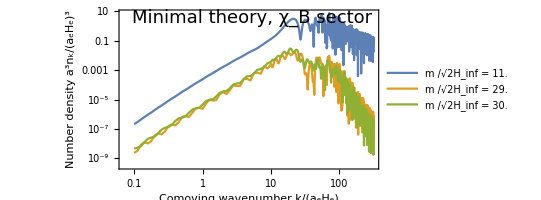

```mathematica
plotRelicSpectrumGeneral[datMinimalScalarRelicCombined,βkSqrBTildeMinimalRelicListList1,"χ_B",{10,-2,-1}]
```

```mathematica
(*idx=2;
Fit[{datMinimalRelicCombined["kListList"][[idx]],(datMinimalRelicCombined["kListList"][[idx]])^3 βkSqrBTildeMinimalRelicListList1[[idx]]}ᵀ[[-200;;-1]]//Log,{1,x},x]*)
```

```mathematica
(*φTildeMinimalRelicPlot1*)
```

```mathematica
(*Show[BTildeMinimalRelicPlot1,PlotRange->{{10^2,10^2.5}//Log,{10^-8,10^4}//Log}]*)
```

```mathematica
(*Range[datMinimalRelicCombined["mList"]//Length]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_scalarMinimalNk_B_1.pdf",BTildeMinimalRelicPlot1];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_BTildeSpectrum_1.pdf",BTildeMinimalRelicPlot1];*)
```

```mathematica
(*subdir="MinimalScalarVarphi";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/mList.csv",datMinimalRelicCombined["mList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/kListList.csv",datMinimalRelicCombined["kListList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrListList.csv",βkSqrφTildeMinimalRelicListList1];*)
```

```mathematica
calculateTotalNumberDensityTemp[dat_,βkSqrTensorListList_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],aT=dat["aT"],ae=1,mϕ=dat["mϕ"],He=dat["He"],Hinf=dat["Hinf"],
a3nListList,lowkCutoff,lowkScale,lowkAmplitude,lowkIndex,highkIndex,highkScale,highkAmplitude,numberOfPoints,f,lowkTotal,highkTotal,midkTotal,total},
a3nListList=Table[kListList[[i]]^3/(2 π^2)βkSqrTensorListList[[i]],{i,Length[mList]}];
lowkCutoff=ae He Exp[-60];
lowkScale=Table[kListList[[i,1]],{i,Length[mList]}];
lowkAmplitude=Table[a3nListList[[i,1]],{i,Length[mList]}];
lowkIndex=Table[(*(Log[a3nListList[[i,25]]]-Log[a3nListList[[i,1]]])/(Log[kListList[[i,25]]]-Log[kListList[[i,1]]])*)3,{i,Length[mList]}];
numberOfPoints=20;
highkIndex=Table[If[mList[[i]]<mϕ,3/2,9/2],{i,Length[mList]}];
highkAmplitude=Table[1/kListList[[i,-1]]^(3/2)Mean[kListList[[i,-numberOfPoints;;-1]]^(highkIndex[[i]](*3/2*))a3nListList[[i,-numberOfPoints;;-1]]],{i,Length[mList]}];
lowkTotal=lowkAmplitude/lowkIndex(1-(lowkCutoff/lowkScale)^lowkIndex);
highkTotal=Table[If[mList[[i]]<mϕ,2/3,2/9],{i,Length[mList]}]*highkAmplitude;
midkTotal=Table[f=Interpolation[{kListList[[i]]//Log,a3nListList[[i]]}ᵀ];
NIntegrate[f[lnk],{lnk,AnnotationValue[f,"Coordinates"][[1,1]],AnnotationValue[f,"Coordinates"][[1,-1]]}],{i,Length[mList]}];
total=lowkTotal+midkTotal+highkTotal;
total
];
```

```mathematica
a3nScalar=calculateTotalNumberDensityTemp[datMinimalScalarRelicCombined,βkSqrBTildeMinimalRelicListList1];
```

```mathematica
(*{Mean[{23.0,25.0,27.0,29.0,30.0}],491/5//N}
{Mean[{3.0,5.0,7.0,9.0,11.0,13.0}],463.5/5//N}*)
```

```mathematica
Fit[{{26.8,98.2},{8.,92.7}},{1,x},x]
```

90.3596+0.292553 x

#### Relic abundance (combined)

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};

mListNormalCollection={{1.0,2.0,3.0,4.0,5.0},{10.0,15.0},{16.0,17.0},{18.0,19.0},{20.0},{21.0},{22.0},{0.2,0.5,0.8},{23.0},{27.0},{20.8},{30.0},{25.0}};
datMinimalCollection=Table[
mListNormal=((√2 Hinf)/He/.Hparams)mListNormalReduced;
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"]
,{mListNormalReduced,mListNormalCollection}];

mListNormal=((√2 Hinf)/He/.Hparams){0.2,0.5,0.8};
kListListNormal=Table[{Table[10^x,{x,-2,-1,0.05}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
AppendTo[datMinimalCollection,loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"]];

mListNormal=((√2 Hinf)/He/.Hparams){0.03,0.1};
kListListNormal=Table[{Table[10^x,{x,-2.5,-1,0.05}],Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
AppendTo[datMinimalCollection,loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"]];

datMinimalRelicCombined=combineDats[datMinimalCollection];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
(*AbsoluteTiming[
tempResult=calculateβkSqrTensorTemp[datMinimalRelicCombined];
]*)
```

```mathematica
(*tensorMinimalRelicPlot=plotRelicSpectrumTensor[datMinimalRelicCombined,tempResult];*)
```

```mathematica
AbsoluteTiming[
βkSqrTensorMinimalRelicListList=calculateβkSqrTensor[datMinimalRelicCombined];
tensorMinimalRelicPlot=plotRelicSpectrumTensor[datMinimalRelicCombined,βkSqrTensorMinimalRelicListList];
]
```

{213.697,Null}

```mathematica
AbsoluteTiming[
βkSqrVectorMinimalRelicListList=calculateβkSqrVector[datMinimalRelicCombined];
vectorMinimalRelicPlot=plotRelicSpectrumVector[datMinimalRelicCombined,βkSqrVectorMinimalRelicListList];
]
```

{235.518,Null}

```mathematica
datMinimalRelicCombined["kListList"][[6;;-1]]//Dimensions
```

{19,891}

```mathematica
(*subdir="MinimalFull";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrTensorListList.csv",βkSqrTensorMinimalRelicListList];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrVectorListList.csv",βkSqrVectorMinimalRelicListList];*)
```

```mathematica
(*subdir="MinimalFull";
βkSqrTensorMinimalRelicListList=Import[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrTensorListList.csv"]/.x_String:>ToExpression[x]//N;
βkSqrVectorMinimalRelicListList=Import[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrVectorListList.csv"]/.x_String:>ToExpression[x]//N;*)
```

```mathematica
(*subdir="MinimalTensor";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/mList.csv",datMinimalRelicCombined["mList"][[6;;-1]]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/kListList.csv",datMinimalRelicCombined["kListList"][[6;;-1]]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrListList.csv",βkSqrTensorMinimalRelicListList[[6;;-1]]];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorMinimalNk_2.pdf",tensorMinimalRelicPlot];*)
```

```mathematica
(*Show[tensorMinimalRelicPlot,PlotRange->{{10^2,10^2.5}//Log,{10^-9,10^-2}//Log}]*)
```

```mathematica
(*datMinimalRelicCombined["mList"]/datMinimalRelicCombined["Hinf"]
datMinimalRelicCombined["mϕ"]/(√2 datMinimalRelicCombined["Hinf"])
datMinimalRelicCombined["HT"]/datMinimalRelicCombined["mList"]*)
```

```mathematica
datMinimalRelicCombined["Hinf"]/GeV
```

1.40791×10^11

```mathematica
a3nTensor=calculateTotalNumberDensity[datMinimalRelicCombined,βkSqrTensorMinimalRelicListList];
a3nVector=calculateTotalNumberDensity[datMinimalRelicCombined,βkSqrVectorMinimalRelicListList];
```

```mathematica
TRH=10^5 GeV;
minIdx=1;maxIdx=-1;
minimalRelicPlot=Block[{mList=datMinimalRelicCombined["mList"][[minIdx;;maxIdx]],He=datMinimalRelicCombined["He"],Hinf=datMinimalRelicCombined["Hinf"],mϕ=datMinimalRelicCombined["mϕ"],ae=1,mListScalar=datMinimalScalarRelicCombined["mList"]},
Ωh2Tensor=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nTensor[[minIdx;;maxIdx]]/(ae^3 He^3));
Ωh2Vector=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nVector[[minIdx;;maxIdx]]/(ae^3 He^3));
Ωh2Scalar=(0.114)(mListScalar/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nScalar/(ae^3 He^3));
ListLogLogPlot[{
{mList/(√2 Hinf),Ωh2Tensor}ᵀ,{mList/(√2 Hinf),Ωh2Vector}ᵀ,{mListScalar/(√2 Hinf),Ωh2Scalar}ᵀ
(*Table[{10^logm,0.12},{logm,Log[10,{Min[mList/Hinf],Max[mList/Hinf]}]}]*)
},
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"Ωh^2",""},{"m /√2H_inf","Relic Abundance (Minimal Theory)"}},
GridLines->None,
PlotRange->{{0.95,1.05Max[mList/(√2 Hinf)]},{10^-3.5,10^2.5}},
PlotLegends->Placed[LineLegend[{"Tensor","Vector","Scalar","Constant 0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
(*Text[Style["T_RH = "~~ToString[NumberForm[TRH/GeV,ScientificNotationThreshold->{-1,1}],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.6,0.4}],{-1,0}],*)
(*{Dashed,Gray,Line[{{1,0.0001}//Log,{1,1000}//Log}]},
Text[Style["Higuchi bound",{Gray, FontFamily->fontfam,FontSize->15}],Scaled[{0.32,0.9}],{-1,0}],*)
{Dashed,Gray,Line[{{mϕ/(√2 Hinf),0.0001}//Log,{mϕ/(√2 Hinf),1000}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.9,0.9}],{-1,0}],
}]
];
```

```mathematica
(*Block[{mList=datMinimalRelicCombined["mList"][[minIdx;;maxIdx]],He=datMinimalRelicCombined["He"],Hinf=datMinimalRelicCombined["Hinf"],mϕ=datMinimalRelicCombined["mϕ"],ae=1,mListScalar=datMinimalScalarRelicCombined["mList"]},
Export[NotebookDirectory[]<>"./SummaryDat/RelicAbundance/"<>"MinimalTensor.csv",{mList/(√2 Hinf),Ωh2Tensor}ᵀ];
Export[NotebookDirectory[]<>"./SummaryDat/RelicAbundance/"<>"MinimalVector.csv",{mList/(√2 Hinf),Ωh2Vector}ᵀ];
Export[NotebookDirectory[]<>"./SummaryDat/RelicAbundance/"<>"MinimalScalar.csv",{mListScalar/(√2 Hinf),Ωh2Scalar}ᵀ];
];*)
```

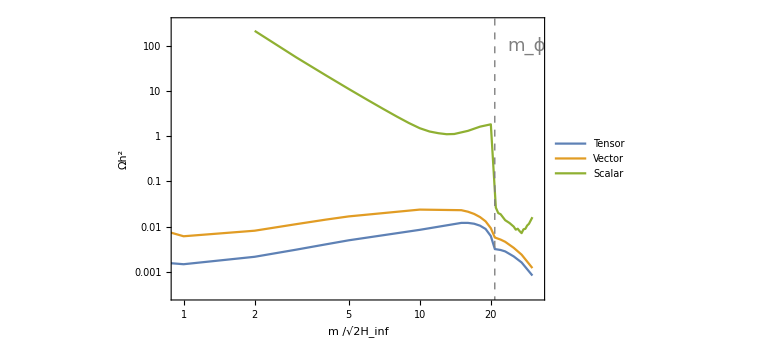

```mathematica
minimalRelicPlot
```

```mathematica
(*ListLogPlot[{datMinimalScalarRelicCombined[["mList"]]/(√2 datMinimalScalarRelicCombined[["Hinf"]]),Ωh2Scalar}ᵀ[[-15;;-1]]]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_minimalRelic.pdf",minimalRelicPlot];*)
```

```mathematica
(*1/(√2 datMinimalRelicCombined["Hinf"])datMinimalScalarRelicCombined["mList"]*)
```

```mathematica
(*1/(√2 datMinimalRelicCombined["Hinf"])datMinimalRelicCombined["mList"]*)
```

```mathematica
√(1-((31.17 √2 datMinimalRelicCombined["Hinf"])/(1.5datMinimalRelicCombined["mϕ"]))^2)
```

0.021098

timing dat for minimal tensor+vector

```mathematica
timingdat={{20,10365+17033},{21,10770+17869},{22,11117+18525},{23,19359+11604},{27,13181+22405}};
1/3600 Evaluate[Fit[timingdat,{1,x},x]]/.x->30
```

10.8591

```mathematica
(*tempf=Interpolation[{datMinimalRelicCombined["mList"]/(√2 datMinimalRelicCombined["Hinf"]),Ωh2Tensor//Log}ᵀ,InterpolationOrder->1]*)
```

```mathematica
(*Plot[tempf[x]//Exp,{x,0.05,30},PlotRange->Full]*)
```

The raise at low-m is because the low-k tail of the spectrum tilts red, and the integral of the spectrum diverges as the index cross 0.

```mathematica
(*Ωh2Tensor/TRH==0.12/TRH*)
```

```mathematica
(*TRH/GeV==(10^5 GeV)/GeV 0.12/Ωh2Tensor*)
```

```mathematica
observedRelic=0.12;
minIdx=1;maxIdx=-1;
minimalTRHPlot=Block[{mList=datMinimalRelicCombined["mList"][[minIdx;;maxIdx]],He=datMinimalRelicCombined["He"],Hinf=datMinimalRelicCombined["Hinf"],mϕ=datMinimalRelicCombined["mϕ"],ae=1,mListScalar=datMinimalScalarRelicCombined["mList"]},
(*TRHCalculated=observedRelic/(2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nTensor[[minIdx;;maxIdx]]/(ae^3 He^3))+2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nVector[[minIdx;;maxIdx]]/(ae^3 He^3)));*)
logΩh2TensorFunc=Interpolation[{mList/(√2 Hinf),Ωh2Tensor//Log}ᵀ,InterpolationOrder->1];
logΩh2VectorFunc=Interpolation[{mList/(√2 Hinf),Ωh2Vector//Log}ᵀ,InterpolationOrder->1];
logΩh2ScalarFunc=Interpolation[{mListScalar/(√2 Hinf),Ωh2Scalar//Log}ᵀ,InterpolationOrder->1];
mOverHDList=Range[1/(√2 Hinf)Max[Min[mList],Min[mListScalar]],1/(√2 Hinf)Min[Max[mList],Max[mListScalar]],0.1];
TRHCalculated=observedRelic/Table[Exp[logΩh2TensorFunc[mOverHD]]+Exp[logΩh2VectorFunc[mOverHD]]+Exp[logΩh2ScalarFunc[mOverHD]],{mOverHD,mOverHDList}];
ListLogLogPlot[(*{mList/Hinf,1/GeV TRHCalculated}ᵀ*){mOverHDList,(10^5 GeV)/GeV TRHCalculated}ᵀ,
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"T_RH [GeV]",""},{"m /√2H_inf","Constraints (Minimal theory)"}},
(*GridLines->Full,*)
PlotRange->{{Min[mOverHDList],Max[mOverHDList]},{10^1.5,10^6.5}},
PlotStyle->Red,
(*PlotLegends->Placed[LineLegend[{"Ωh^2=0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],*)
ImageSize->Large,
Epilog->{
(*Text[Style["Minimal Theory",{FontFamily->fontfam,FontSize->18}],Scaled[{0.6,0.2}],{-1,0}],*)
(*{Dashed,Gray,Line[{{√2,10^-1}//Log,{√2,10^7}//Log}]},
Text[Style["Higuchi bound",{Gray, FontFamily->fontfam,FontSize->15}],Scaled[{0.32,0.2}],{-1,0}],*)
{Dashed,Gray,Line[{{mϕ/(√2 Hinf),10^-1}//Log,{mϕ/(√2 Hinf),10^7}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.88,0.2}],{-1,0}],
{Lighter[Red],Arrowheads[0.05],Thickness[0.01],Arrow[{{10,10^3.9}//Log,{10,10^3}//Log}]},
Text[Style["Ωh^2 ⩽ 0.12",{Lighter[Red], FontFamily->fontfam,FontSize->18}],Scaled[{0.58,0.28}],{-1,0}],
},
Filling->Top,
FillingStyle->Directive[Opacity[0.5],Gray](*PatternFilling["Checkerboard"]*)(*HatchFilling["Diagonal"]*)
]
];
```

```mathematica
(*datMinimalScalarRelicCombined["mList"]/(√2 datMinimalScalarRelicCombined["Hinf"])*)
```

```mathematica
(*(0.114)((10 √2 datMinimalScalarRelicCombined["Hinf"])/(10^10 GeV))(datMinimalScalarRelicCombined["He"]/(10^10 GeV))((10^4 GeV)/(10^8 GeV))(a3nScalar[[9]]/datMinimalScalarRelicCombined["He"]^3)*)
```

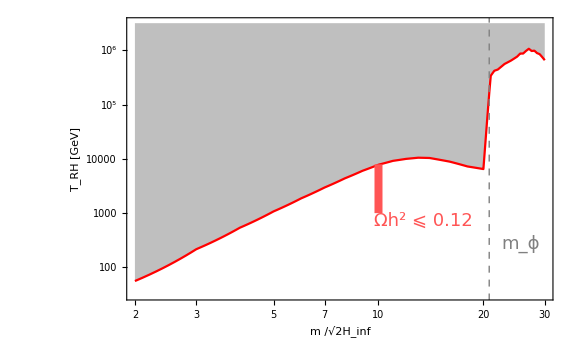

```mathematica
minimalTRHPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"./SummaryDat/"<>"fig_5.csv",{mOverHDList,(10^5 GeV)/GeV TRHCalculated}ᵀ];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_minimalTRH.pdf",minimalTRHPlot];*)
```

```mathematica
tensorMinimalRelicPlot1=plotRelicSpectrumGeneral[datMinimalRelicCombined,βkSqrTensorMinimalRelicListList,"tensor",{4,9,15,16}];
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorMinimalNk_1.pdf",tensorMinimalRelicPlot1];*)
```

```mathematica
vectorMinimalRelicPlot1=plotRelicSpectrumGeneral[datMinimalRelicCombined,βkSqrVectorMinimalRelicListList,"vector",{4,9,15,16}];
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorMinimalNk_1.pdf",vectorMinimalRelicPlot1];*)
```

```mathematica
datMinimalRelicCombined["Hinf"]/GeV
```

1.40791×10^11

#### Relic abundance combined (Non-minimal)

```mathematica
(*subdir="NonMinimalFull";
βkSqrTensorNonMinimalRelicListList=Import[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrTensorListList.csv"]/.x_String:>ToExpression[x]//N;
βkSqrVectorNonMinimalRelicListList=Import[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrVectorListList.csv"]/.x_String:>ToExpression[x]//N;
βkSqrScalarNonMinimal=Import[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrScalarListList.csv"]/.x_String:>ToExpression[x]//N;*)
```

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};

mListNormalCollection={{2.0,5.0,8.0,11.0,14.0,17.0,19.0,20.0,20.5,21.0},{22.0},{25.0,28.0},{30.0}};
datNonMinimalCollection=Table[
mListNormal=((√2 Hinf)/He/.Hparams)mListNormalReduced;
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
loadDat[60,"H",200,mListNormal,kListListNormal,"Non-Minimal"]
,{mListNormalReduced,mListNormalCollection}];

datNonMinimalRelicCombined=combineDats[datNonMinimalCollection];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

```mathematica
AbsoluteTiming[
βkSqrTensorNonMinimalRelicListList=calculateβkSqrTensor[datNonMinimalRelicCombined];
tensorNonMinimalRelicPlot=plotRelicSpectrumTensor[datNonMinimalRelicCombined,βkSqrTensorNonMinimalRelicListList];
]
```

{1.21194,Null}

```mathematica
AbsoluteTiming[
βkSqrVectorNonMinimalRelicListList=calculateβkSqrVector[datNonMinimalRelicCombined];
vectorNonMinimalRelicPlot=plotRelicSpectrumVector[datNonMinimalRelicCombined,βkSqrVectorNonMinimalRelicListList];
]
```

$Aborted

```mathematica
a3nTensorNonMinimal=calculateTotalNumberDensity[datNonMinimalRelicCombined,βkSqrTensorNonMinimalRelicListList];
a3nVectorNonMinimal=calculateTotalNumberDensity[datNonMinimalRelicCombined,βkSqrVectorNonMinimalRelicListList];
```

Scalar sector data

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};

mListNormalCollection={{7.0},{11.0},{14.0},{17.0},{20.0},{9.0},{8.0,10.0},{12.0},{19.0},{6.4,28.0}};
tempCollection1=Table[
mListNormal=((√2 Hinf)/He/.Hparams)mListNormalReduced;
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
loadDat[60,"H",200,mListNormal,kListListNormal,"Non-Minimal"]
,{mListNormalReduced,mListNormalCollection}];

midpointList={520,480,480};
mListNormalCollection={{21.0},{25.0},{30.0}};
kListNormalRelic={Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort;
tempCollection2=Table[
mListNormal=((√2 Hinf)/He/.Hparams)mListNormalCollection[[i]];
{loadDat[60,"H",200,mListNormal,{kListNormalRelic[[1;;midpointList[[i]]]]},"Non-Minimal"],loadDat[60,"H",200,mListNormal,{kListNormalRelic[[midpointList[[i]]+1;;-1]]},"Non-Minimal"]},{i,Length[mListNormalCollection]}]//Flatten;

datNonMinimalScalarCollection=Join[tempCollection1,tempCollection2];
datNonMinimalScalarRelicCombined=combineDats[datNonMinimalScalarCollection];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

```mathematica
AbsoluteTiming[
βkSqrScalarNonMinimal=calculateβkSqrScalar[datNonMinimalScalarRelicCombined];
scalarNonMinimalPlot=plotRelicSpectrumScalar[datNonMinimalScalarRelicCombined,βkSqrScalarNonMinimal];
]
```

{1601.2,Null}

```mathematica
(*subdir="NonMinimalFull";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrTensorListList.csv",βkSqrTensorNonMinimalRelicListList];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrVectorListList.csv",βkSqrVectorNonMinimalRelicListList];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrScalarListList.csv",βkSqrScalarNonMinimal];*)
```

```mathematica
(*scalarNonMinimalRelicPlot1=plotRelicSpectrumGeneral[datNonMinimalScalarRelicCombined,βkSqrScalarNonMinimal,"scalar",{1,2,5,6}];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_scalarNonMinimalNk_1.pdf",scalarNonMinimalRelicPlot1];*)
```

```mathematica
a3nScalarNonMinimal=calculateTotalNumberDensity[datNonMinimalScalarRelicCombined,βkSqrScalarNonMinimal];
```

```mathematica
(*subdir="NonMinimalScalar";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/mList.csv",datNonMinimalScalarRelicCombined["mList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/kListList.csv",datNonMinimalScalarRelicCombined["kListList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrListList.csv",βkSqrScalarNonMinimal];*)
```

```mathematica
βkSqrScalarNonMinimal//Dimensions
```

{15,891}

```mathematica
datNonMinimalRelicCombined["kListList"]//Dimensions
βkSqrTensorNonMinimalRelicListList//Dimensions
```

{14,891}

{14,891}

```mathematica
(*Show[scalarNonMinimalPlot,PlotRange->{{10^2,10^2.5}//Log,{0.9*10^-12,10^-1}//Log}]*)
```

```mathematica
(*Ωh2Scalar//ListPlot*)
```

```mathematica
a3nTensorLogFunc=Interpolation[{datNonMinimalRelicCombined["mList"]/(√2 datNonMinimalRelicCombined["Hinf"]),a3nTensorNonMinimal}ᵀ//Log,InterpolationOrder->1];
a3nVectorLogFunc=Interpolation[{datNonMinimalRelicCombined["mList"]/(√2 datNonMinimalRelicCombined["Hinf"]),a3nVectorNonMinimal}ᵀ//Log,InterpolationOrder->1];
a3nTensorFunc=Function[t,Exp[a3nTensorLogFunc[t//Log]]];
a3nVectorFunc=Function[t,Exp[a3nVectorLogFunc[t//Log]]];

a3nScalarLogFunc=Interpolation[{datNonMinimalScalarRelicCombined["mList"]/(√2 datNonMinimalScalarRelicCombined["Hinf"]),a3nScalarNonMinimal}ᵀ//Log,InterpolationOrder->1];
a3nScalarFunc=Function[t,Piecewise[{{Exp[a3nScalarLogFunc[t//Log]],Min[datNonMinimalScalarRelicCombined["mList"]/(√2 datNonMinimalScalarRelicCombined["Hinf"])]<t<Max[datNonMinimalScalarRelicCombined["mList"]/(√2 datNonMinimalScalarRelicCombined["Hinf"])]}},0]];
```

```mathematica
(*Plot[fScalar[t],{t,Min[datNonMinimalScalarRelicCombined["mList"]/datNonMinimalScalarRelicCombined["Hinf"]]-1,Max[datNonMinimalScalarRelicCombined["mList"]/datNonMinimalScalarRelicCombined["Hinf"]]+1}]*)
```

```mathematica
(*Table[{t,2fTensor[t]+2fVector[t]+fScalar[t]},{t,Min[datNonMinimalRelicCombined["mList"]/datNonMinimalRelicCombined["Hinf"]],Max[datNonMinimalRelicCombined["mList"]/datNonMinimalRelicCombined["Hinf"]],0.1}]//ListLogLogPlot*)
```

```mathematica
(*LogLogPlot[{fTensor[t],fVector[t]},{t,2.83,31.1},PlotRange->Full]*)
```

Relic abundance plot

```mathematica
TRH=10^5 GeV;
(*minIdx=1;maxIdx=-1;*)
NonminimalRelicPlot=Block[{mList=datNonMinimalRelicCombined["mList"],He=datNonMinimalRelicCombined["He"],Hinf=datNonMinimalRelicCombined["Hinf"],mϕ=datNonMinimalRelicCombined["mϕ"],ae=1,mListScalar=datNonMinimalScalarRelicCombined["mList"]},
Ωh2Tensor=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nTensorNonMinimal/(ae^3 He^3));
Ωh2Vector=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nVectorNonMinimal/(ae^3 He^3));
Ωh2Scalar=(0.114)(mListScalar/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nScalarNonMinimal/(ae^3 He^3));
ListLogLogPlot[{
{mList/(√2 Hinf),Ωh2Tensor}ᵀ,{mList/(√2 Hinf),Ωh2Vector}ᵀ,{mListScalar/(√2 Hinf),Ωh2Scalar}ᵀ
(*Table[{10^logm,0.12},{logm,Log[10,{Min[mList/Hinf],Max[mList/Hinf]}]}]*)
},
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"Ωh^2",""},{"m /√2H_inf","Relic Abundance (Nonminimal Theory)"}},
GridLines->None,
(*PlotRange->Full,*)
PlotLegends->Placed[LineLegend[{"Tensor","Vector","Scalar","T+V"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
(*Text[Style["T_RH = 10^5GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.3,0.2}],{-1,0}]*)
(*Text[Style["T_RH = "~~ToString[NumberForm[TRH/GeV,ScientificNotationThreshold->{-1,1}],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.6,0.75}],{-1,0}],*)
{Dashed,Gray,Line[{{mϕ/(√2 Hinf),10^-5}//Log,{mϕ/(√2 Hinf),1000}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.87,0.9}],{-1,0}]
}]
];
```

```mathematica
(*Block[{mList=datNonMinimalRelicCombined["mList"],He=datNonMinimalRelicCombined["He"],Hinf=datNonMinimalRelicCombined["Hinf"],mϕ=datNonMinimalRelicCombined["mϕ"],ae=1,mListScalar=datNonMinimalScalarRelicCombined["mList"]},
Export[NotebookDirectory[]<>"./SummaryDat/RelicAbundance/"<>"NonMinimalTensor.csv",{mList/(√2 Hinf),Ωh2Tensor}ᵀ];
Export[NotebookDirectory[]<>"./SummaryDat/RelicAbundance/"<>"NonMinimalVector.csv",{mList/(√2 Hinf),Ωh2Vector}ᵀ];
Export[NotebookDirectory[]<>"./SummaryDat/RelicAbundance/"<>"NonMinimalScalar.csv",{mListScalar/(√2 Hinf),Ωh2Scalar}ᵀ];
]*)
```

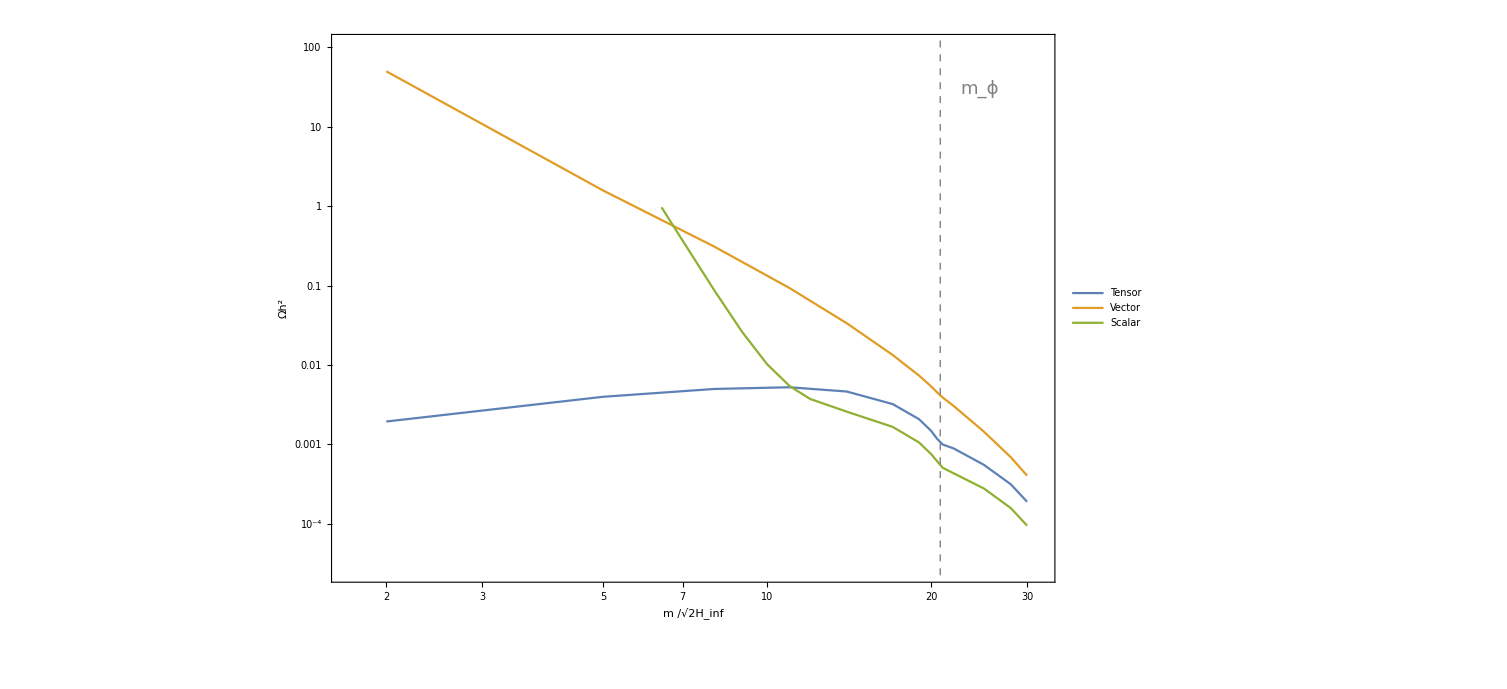

```mathematica
NonminimalRelicPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_NonminimalRelic.pdf",NonminimalRelicPlot];*)
```

```mathematica
{datNonMinimalRelicCombined["mList"]/datNonMinimalRelicCombined["Hinf"],datNonMinimalScalarRelicCombined["mList"]/datNonMinimalScalarRelicCombined["Hinf"]}/√2
```

{{2.,5.,8.,11.,14.,17.,19.,20.,20.5,21.,22.,25.,28.,30.},{6.4,7.,8.,9.,10.,11.,12.,14.,17.,19.,20.,21.,25.,28.,30.}}

timing for nonminimal scalar

```mathematica
timingdat={{7,37319},{11,48950},{14,57238},{17,66467},{20,75763}};
fScalar[y_]:=1/3600 Evaluate[Fit[timingdat,{1,x},x]]/.x->y;
```

laptop factor = 2.53

```mathematica
{(108648/3600)/11.9438,(131351/3600)/14.400331279723305}
```

{2.52683,2.53372}

```mathematica
fScalar[20]*2.53
```

53.0065

campus factor = 2.06

```mathematica
{(176930/3600)/(fScalar[8]+fScalar[10]),(278323/3600)/(fScalar[6.4]+fScalar[28])}
```

{2.05744,2.07177}

```mathematica
6+3*24
```

78

TRH plot

```mathematica
(*Subdivide[1//Log,101//Log,1000]//Exp//N*)
```

```mathematica
observedRelic=0.12;
NonminimalTRHPlot=Block[{mList=datNonMinimalRelicCombined["mList"],He=datNonMinimalRelicCombined["He"],Hinf=datNonMinimalRelicCombined["Hinf"],mϕ=datNonMinimalRelicCombined["mϕ"],ae=1,mListPlot,a3nTensorNonMinimal,a3nVectorNonMinimal,a3nScalarNonMinimal},
mListPlot=Subdivide[Min[mList]//Log,Max[mList]//Log,1000]//Exp;
a3nTensorNonMinimal=Table[a3nTensorFunc[m/(√2 Hinf)],{m,mListPlot}];
a3nVectorNonMinimal=Table[a3nVectorFunc[m/(√2 Hinf)],{m,mListPlot}];
a3nScalarNonMinimal=Table[a3nScalarFunc[m/(√2 Hinf)],{m,mListPlot}];
TRHCalculated=observedRelic/((0.114)(mListPlot/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))((2*a3nTensorNonMinimal+2*a3nVectorNonMinimal+a3nScalarNonMinimal)/(ae^3 He^3)));
exportDat={mListPlot/(√2 Hinf),1/GeV TRHCalculated}ᵀ;
ListLogLogPlot[{mListPlot/(√2 Hinf),1/GeV TRHCalculated}ᵀ,
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"T_RH [GeV]",""},{"m /√2H_inf","Constraints (Nonminimal theory)"}},
(*PlotLegends->Placed[LineLegend[{"(Ω_T+Ω_V+Ω_S)h^2=0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],*)
PlotRange->{{(*mListPlot/(√2 Hinf)//Min*)6.45,mListPlot/(√2 Hinf)//Max},{10^3.5,10^7.5}},
PlotStyle->Red,
ImageSize->Large,
Epilog->{
{Dashed,Gray,Line[{{mϕ/(√2 Hinf),10^-1}//Log,{mϕ/(√2 Hinf),10^9}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.8,0.2}],{-1,0}],
{Lighter[Red],Arrowheads[0.05],Thickness[0.01],Arrow[{{15,10^5.6}//Log,{15,10^4.8}//Log}]},
Text[Style["ΩSuperscriptBox[StyleBox[\"h\",FontSlant->\"Italic\"], \"2\"] ⩽ 0.12",{Lighter[Red], FontFamily->fontfam,FontSize->18}],Scaled[{0.54,0.29}],{-1,0}],
(*{Dashed,Gray,Line[{{6.4,10^-1}//Log,{6.4,10^9}//Log}]},
Text[Style["scalar cutoff",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.24,0.2}],{-1,0}],*)
},
Filling->Top,
FillingStyle->Directive[Opacity[0.5],Gray]
]
];
```

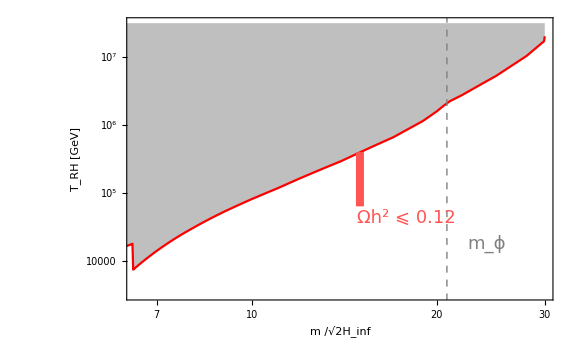

```mathematica
NonminimalTRHPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"./SummaryDat/"<>"fig_8.csv",exportDat];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_NonminimalTRH.pdf",NonminimalTRHPlot];*)
```

```mathematica
(*observedRelic=0.12;
minIdx=1;maxIdx=-1;
NonminimalTRHPlot=Block[{mList=datNonMinimalRelicCombined["mList"][[minIdx;;maxIdx]],He=datNonMinimalRelicCombined["He"],Hinf=datNonMinimalRelicCombined["Hinf"],mϕ=datNonMinimalRelicCombined["mϕ"],ae=1},
TRHCalculated=observedRelic/(2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nTensorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3))+2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nVectorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3)));
ListLogLogPlot[{mList/Hinf,1/GeV TRHCalculated}ᵀ,
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"T_RH [GeV]",""},{"m/H_inf","Reheating Temperature (Non-Minimal theory)"}},
PlotLegends->Placed[LineLegend[{"(Ω_T+Ω_V)h^2=0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
{Dashed,Gray,Line[{{mϕ/Hinf,10^-1}//Log,{mϕ/Hinf,10^7}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.9,0.2}],{-1,0}],
{Lighter[Blue],Arrowheads[0.05],Thickness[0.01],Arrow[{{10,10^4.4}//Log,{10,10^3.5}//Log}]},
Text[Style["Ωh^2 ⩽ 0.12",{Lighter[Blue], FontFamily->fontfam,FontSize->18}],Scaled[{0.47,0.29}],{-1,0}],
},
Filling->Top,
FillingStyle->Directive[Opacity[0.5],Gray]
]
];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_NonminimalTRH.pdf",NonminimalTRHPlot];*)
```

#### Relic abundance 1 (Non-minimal)

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){2.0,5.0,8.0,11.0,14.0,17.0,19.0,20.0,20.5,21.0};
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
datNonMinimalRelic1=loadDat[60,"H",200,mListNormal,kListListNormal,"Non-Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
βkSqrTensorNonMinimalRelicListList1=calculateβkSqrTensor[datNonMinimalRelic1];
```

```mathematica
tensorNonMinimalRelicPlot1=plotRelicSpectrumTensor[datNonMinimalRelic1,βkSqrTensorNonMinimalRelicListList1];
```

```mathematica
βkSqrVectorNonMinimalRelicListList1=calculateβkSqrVector[datNonMinimalRelic1];
```

```mathematica
vectorNonMinimalRelicPlot1=plotRelicSpectrumVector[datNonMinimalRelic1,βkSqrVectorNonMinimalRelicListList1];
```

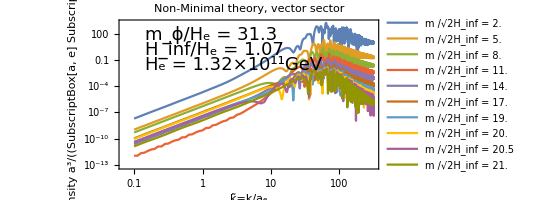

```mathematica
vectorNonMinimalRelicPlot1
```

```mathematica
(*tempPlot=Show[vectorNonMinimalRelicPlot1,PlotRange->{{10^1,10^2.5}//Log,{10^-8,10^4}//Log}]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorNonMinimalNk_Relic_1.pdf",vectorNonMinimalRelicPlot1];*)
```

```mathematica
(*tempPlot=Show[tensorNonMinimalRelicPlot1,PlotRange->{{10^1.5,10^2.5}//Log,{10^-8,10^-1.5}//Log}]*)
```

```mathematica
a3nTensorNonMinimal=calculateTotalNumberDensity[datNonMinimalRelic1,βkSqrTensorNonMinimalRelicListList1];
a3nVectorNonMinimal=calculateTotalNumberDensity[datNonMinimalRelic1,βkSqrVectorNonMinimalRelicListList1];
```

```mathematica
TRH=10^5 GeV;
minIdx=1;maxIdx=-1;
NonminimalRelicPlot=Block[{mList=datNonMinimalRelic1["mList"][[minIdx;;maxIdx]],He=datNonMinimalRelic1["He"],Hinf=datNonMinimalRelic1["Hinf"],mϕ=datNonMinimalRelic1["mϕ"],ae=1},
Ωh2Tensor=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nTensorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3));
Ωh2Vector=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nVectorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3));
ListLogLogPlot[{
{mList/Hinf,Ωh2Tensor}ᵀ,{mList/Hinf,Ωh2Vector}ᵀ,{mList/Hinf,Ωh2Tensor+Ωh2Vector}ᵀ
(*Table[{10^logm,0.12},{logm,Log[10,{Min[mList/Hinf],Max[mList/Hinf]}]}]*)
},
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"Ωh^2",""},{"m/H_inf","Relic Abundance (Non-Minimal Theory)"}},
GridLines->None,
(*PlotRange->Full,*)
PlotLegends->Placed[LineLegend[{"Tensor","Vector","T+V","Constant 0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
(*Text[Style["T_RH = 10^5GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.3,0.2}],{-1,0}]*)
Text[Style["T_RH = "~~ToString[NumberForm[TRH/GeV,ScientificNotationThreshold->{-1,1}],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.6,0.15}],{-1,0}],
{Dashed,Gray,Line[{{mϕ/Hinf,0.0001}//Log,{mϕ/Hinf,1000}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.9,0.9}],{-1,0}]
}]
];
```

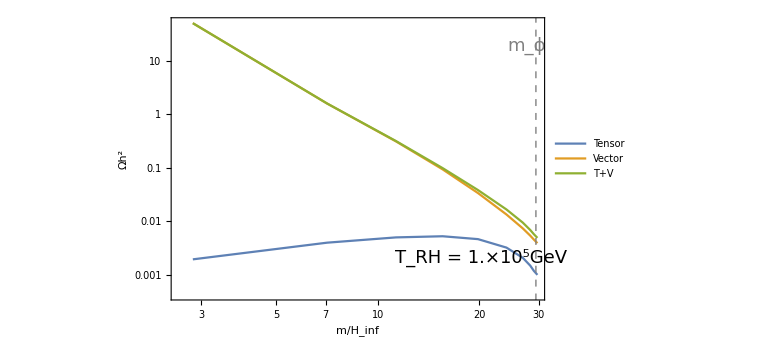

```mathematica
NonminimalRelicPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_NonminimalRelic.pdf",NonminimalRelicPlot];*)
```

```mathematica
tensorNonMinimalRelicPlot1=plotRelicSpectrumGeneral[datNonMinimalRelic1,βkSqrTensorNonMinimalRelicListList1,"tensor",{1,4,8,10}];
```

```mathematica
Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorNonMinimalNk_1.pdf",tensorNonMinimalRelicPlot1];
```

```mathematica
vectorNonMinimalRelicPlot1=plotRelicSpectrumGeneral[datNonMinimalRelic1,βkSqrVectorNonMinimalRelicListList1,"vector",{1,4,8,10}];
```

```mathematica
Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorNonMinimalNk_1.pdf",vectorNonMinimalRelicPlot1];
```

TRH plot

```mathematica
observedRelic=0.12;
minIdx=1;maxIdx=-1;
NonminimalTRHPlot=Block[{mList=datNonMinimalRelic1["mList"][[minIdx;;maxIdx]],He=datNonMinimalRelic1["He"],Hinf=datNonMinimalRelic1["Hinf"],mϕ=datNonMinimalRelic1["mϕ"],ae=1},
TRHCalculated=observedRelic/(2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nTensorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3))+2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nVectorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3)));
ListLogLogPlot[{mList/Hinf,1/GeV TRHCalculated}ᵀ,
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"T_RH [GeV]",""},{"m/H_inf","Reheating Temperature (Non-Minimal theory)"}},
(*GridLines->Full,*)
(*PlotRange->Full,*)
PlotLegends->Placed[LineLegend[{"(Ω_T+Ω_V)h^2=0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
{Dashed,Gray,Line[{{mϕ/Hinf,10^-1}//Log,{mϕ/Hinf,10^7}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.9,0.2}],{-1,0}],
{Lighter[Blue],Arrowheads[0.05],Thickness[0.01],Arrow[{{10,10^4.4}//Log,{10,10^3.5}//Log}]},
Text[Style["Ωh^2 ⩽ 0.12",{Lighter[Blue], FontFamily->fontfam,FontSize->18}],Scaled[{0.47,0.29}],{-1,0}],
},
Filling->Top,
FillingStyle->Directive[Opacity[0.5],Gray](*PatternFilling["Checkerboard"]*)(*HatchFilling["Diagonal"]*)
]
];
```

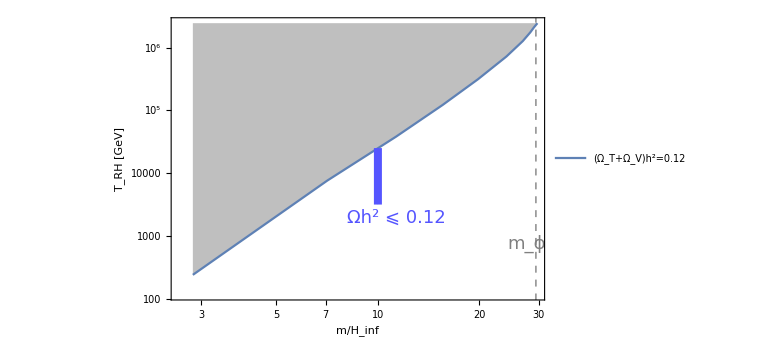

```mathematica
NonminimalTRHPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_NonminimalTRH.pdf",NonminimalTRHPlot];*)
```

```mathematica
(*observedRelic=0.12;
minIdx=1;maxIdx=-1;
NonminimalTRHPlot=Block[{mList=datNonMinimalRelic1["mList"][[minIdx;;maxIdx]],He=datNonMinimalRelic1["He"],Hinf=datNonMinimalRelic1["Hinf"],mϕ=datNonMinimalRelic1["mϕ"],ae=1},
TRHCalculated=observedRelic/(2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nTensorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3))+2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(1/(10^8 GeV))(a3nVectorNonMinimal[[minIdx;;maxIdx]]/(ae^3 He^3)));
ListLogLogPlot[{mList/Hinf,1/GeV TRHCalculated}ᵀ,
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{"m/H_inf","T_RH [GeV]"},
PlotLegends->Placed[LineLegend[{"Ω_T+Ω_V=0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
Text[Style["Non-Minimal Theory",{FontFamily->fontfam,FontSize->18}],Scaled[{0.6,0.2}],{-1,0}],
{Dashed,Gray,Line[{{mϕ/Hinf,10^-1}//Log,{mϕ/Hinf,10^7}//Log}]},
Text[Style["m_ϕ",{Gray, FontFamily->fontfam,FontSize->18}],Scaled[{0.9,0.9}],{-1,0}],
}]
];*)
```

#### Inflaton perturbation only

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){2.0};
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
datInflaton=loadDat[60,"H",200,mListNormal,kListListNormal,"InflatonPerturbation"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
datInflaton["TSectorFinal"]//Dimensions
```

{391,2}

```mathematica
βkSqrInflaton=calculateβkSqrInflaton[datInflaton];
βkSqrInflatonNonlinear=βkSqrInflaton[[1]];
βkSqrInflatonQuadratic=βkSqrInflaton[[2]];
```

```mathematica
inflatonNonlinearPlot=plotRelicSpectrumGeneral[datInflaton,βkSqrInflatonNonlinear,"Nonlinear",{1}];
inflatonQuadraticPlot=plotRelicSpectrumGeneral[datInflaton,βkSqrInflatonQuadratic,"Quadratic",{1}];
```

```mathematica
βkSqrInflatonNonlinear//Dimensions
```

{1,391}

```mathematica
(*βkSqrInflatonNonlinear*)
```

```mathematica
(*subdir="VarphiU";
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/mList.csv",datInflaton["mList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/kListList.csv",datInflaton["kListList"]];
Export[NotebookDirectory[]<>"SummaryDat/"~~subdir~~"/betaSqrListList.csv",βkSqrInflatonNonlinear];*)
```

```mathematica
compareInflatonPerturbationPlot=Block[{kListListFull=datMinimalRelicCombined["kListList"],kListListPartial=datInflaton["kListList"],aT=datInflaton["aT"],ae=1,mϕ=datInflaton["mϕ"],He=datInflaton["He"],Hinf=datInflaton["Hinf"],
nListListFull,nListListNonlinear,nListListQuadratic,epilog,
βkSqrListListFull=βkSqrφTildeMinimalRelicListList1,βkSqrListListNonlinear=βkSqrInflatonNonlinear,βkSqrListListQuadratic=βkSqrInflatonQuadratic},
nListListFull=Table[aT^-3 kListListFull[[i]]^3/(2 π^2)βkSqrListListFull[[i]],{i,1}];
nListListNonlinear=Table[aT^-3 kListListPartial[[i]]^3/(2 π^2)βkSqrListListNonlinear[[i]],{i,1}];
nListListQuadratic=Table[aT^-3 kListListPartial[[i]]^3/(2 π^2)βkSqrListListQuadratic[[i]],{i,1}];
epilog={
Text[Style["Inflaton perturbation",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],Scaled[{0.05,0.95}],{-1,0}],
};
ListLogLogPlot[{{kListListFull[[1]]/He,aT^3 nListListFull[[1]]/(ae^3 He^3)}ᵀ,{kListListPartial[[1]]/He,aT^3 nListListNonlinear[[1]]/(ae^3 He^3)}ᵀ,{kListListPartial[[1]]/He,aT^3 nListListQuadratic[[1]]/(ae^3 He^3)}ᵀ},
Frame->True,FrameLabel->{"Comoving wavenumber  k/(a_eH_e)","Number density  a^3n_k/(a_eH_e)^3"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLegends->Placed[LineLegend[{"Full theory (2 dof)","Nonlinear (m_eff^2 = V''(ϕ)...)","Quadratic (m_eff^2 = m_ϕ^2...)"},LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Bottom}],
PlotRange->Full,AspectRatio->1/2,
Epilog->epilog,
Joined->True,GridLines->None,ImageSize->Full]
];
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_compareInflatonPerturbation.pdf",compareInflatonPerturbationPlot];*)
```

## Study of low-k behavior

#### Test for range ν (Minimal)

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
(*mListNormal=(Hinf/He/.Hparams)({0.1,0.3,1,Range[1.3,1.6,0.01]}//Flatten);
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-2,-1,0.2}];*)
mListNormal=(Hinf/He/.Hparams)Range[0.5,3.0,0.01];
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-2.5,-2.0,0.1}];
datMinimalPowerLaw=loadDat[60,"H",100,mListNormal,kListListNormal,"Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
βkSqrTensorListListPL=calculateβkSqrTensor[datMinimalPowerLaw];
```

```mathematica
βkSqrVectorListListPL=calculateβkSqrVector[datMinimalPowerLaw];
```

```mathematica
(*tensorMinimalPlotTensor4=plotRelicSpectrumTensor[datMinimalTensorPowerLaw,βkSqrTensorListList4];*)
```

```mathematica
dlogk=datMinimalPowerLaw["kListList"][[1,2]]/datMinimalPowerLaw["kListList"][[1,1]]//Log
```

0.230259

```mathematica
dlogβkListTensor=Table[βkSqrTensorListListPL[[i,2]]/βkSqrTensorListListPL[[i,1]]//Log,{i,Length[datMinimalPowerLaw["mList"]]}];
```

```mathematica
dlogβkListVector=Table[βkSqrVectorListListPL[[i,2]]/βkSqrVectorListListPL[[i,1]]//Log,{i,Length[datMinimalPowerLaw["mList"]]}];
```

```mathematica
2((1/2-ν)-1/2)/.ν->√(1/4-γ)/.γ->(mOverHinf^2-2)
```

-2 √(9/4-mOverHinf^2)

```mathematica
βkSqrTensorListListPL[[-1]]//Log
```

{-5.49731,-5.50089,-5.51128,-5.51532,-5.50781,-5.49838}

```mathematica
datMinimalPowerLaw["kListListNormal"][[-1]]//Log
```

{-5.75646,-5.5262,-5.29595,-5.06569,-4.83543,-4.60517}

```mathematica
predictedIndex=Table[{mOverHinf,2((1/2-ν)-1/2)/.ν->√(1/4-γ)}/.γ->(mOverHinf^2-2),{mOverHinf,0.5,1.6,0.01}];
```

```mathematica
fitted=Table[LinearModelFit[{datMinimalPowerLaw["kListListNormal"][[i]]//Log,βkSqrTensorListListPL[[i]]//Log}ᵀ,x,x],{i,Length[datMinimalPowerLaw["mList"]]}];
```

```mathematica
datMinimalPowerLaw["kListList"][[1]]//Log
```

{-22.4856,-22.2554,-22.0251,-21.7948,-21.5646,-21.3343}

```mathematica
Log[datMinimalPowerLaw["He"]]
```

-16.7292

```mathematica
fitted//Length
```

251

```mathematica
(datMinimalPowerLaw["mList"][[115]])/datMinimalPowerLaw["Hinf"]
```

1.64

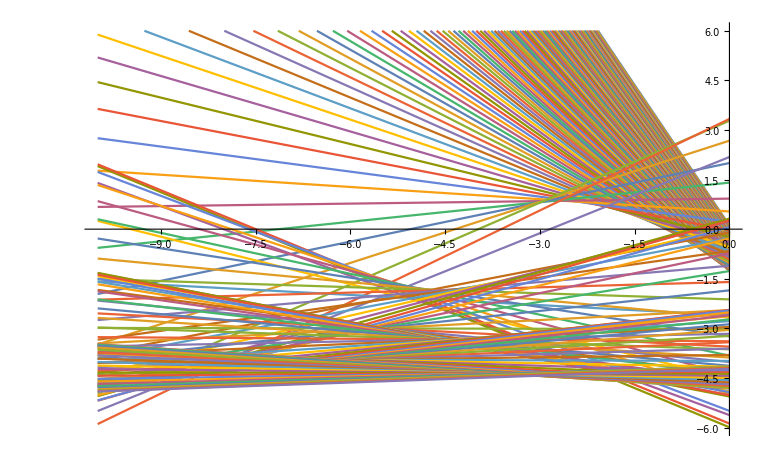

```mathematica
Plot[Evaluate[Normal[fitted[[1;;200]]]],{x,-10,0},PlotRange->{{-10,0},{-6,6}}]
```

```mathematica
Log[10,Exp[-7]]//N
```

-3.04006

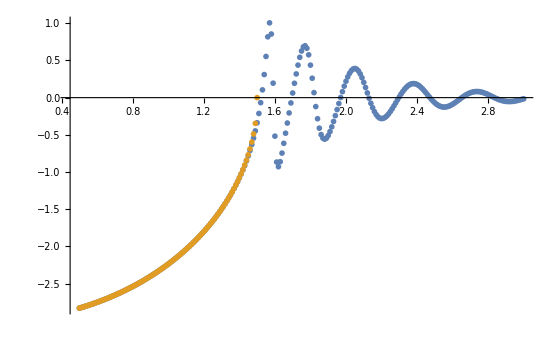

```mathematica
ListPlot[{{datMinimalPowerLaw["mList"]/datMinimalPowerLaw["Hinf"],dlogβkListTensor/dlogk}ᵀ,predictedIndex},PlotRange->Full,Joined->{False,False}]
```

```mathematica
(*vectorMinimalPlotVector4=plotRelicSpectrumVector[datMinimalTensorPowerLaw,βkSqrVectorListList4];*)
```

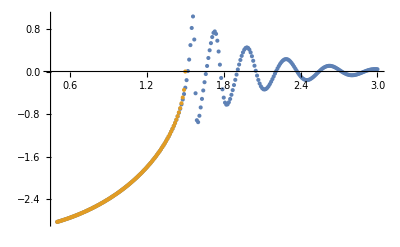

```mathematica
ListPlot[{{datMinimalPowerLaw["mList"]/datMinimalPowerLaw["Hinf"],dlogβkListVector/dlogk}ᵀ,predictedIndex},PlotRange->Full]
```

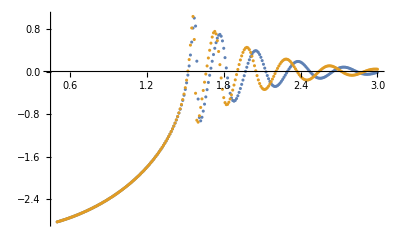

```mathematica
ListPlot[{{datMinimalPowerLaw["mList"]/datMinimalPowerLaw["Hinf"],dlogβkListTensor/dlogk}ᵀ,{datMinimalPowerLaw["mList"]/datMinimalPowerLaw["Hinf"],dlogβkListVector/dlogk}ᵀ},PlotRange->Full]
```

## Old test imports

#### Test high-T high-k

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){2.0};
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
datMinimalHighT=loadDat[60,"H",600,mListNormal,kListListNormal,"Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
datMinimalHighT["aT"]
```

1401.73

```mathematica
datMinimalRelicCombined["aT"]
```

676.419

```mathematica
676*3^(2/3)//N
```

1406.14

```mathematica
(100datMinimalHighT["He"])/(datMinimalHighT["aT"]datMinimalHighT["mϕ"])
```

0.00227835

```mathematica
datMinimalHighT["mϕ"]/datMinimalHighT["He"]
```

31.3123

```mathematica
βkSqrScalarMinimalHighTListList1=calculateβkSqrScalar[datMinimalHighT];
βkSqrφTildeMinimalHighTListList1=βkSqrScalarMinimalHighTListList1[[1;;-1,1;;-1,1]];
βkSqrBTildeMinimalHighTListList1=βkSqrScalarMinimalHighTListList1[[1;;-1,1;;-1,2]];
```

```mathematica
φTildeMinimalHighTPlot1=plotRelicSpectrumGeneral[datMinimalHighT,βkSqrφTildeMinimalHighTListList1,"χ_φ",{1}];
BTildeMinimalHighTPlot1=plotRelicSpectrumGeneral[datMinimalHighT,βkSqrBTildeMinimalHighTListList1,"χ_B",{1}];
```

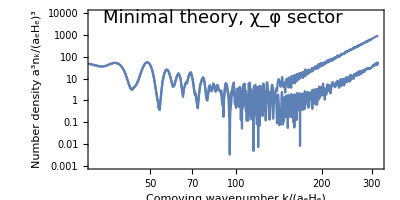

```mathematica
Show[{φTildeMinimalRelicPlot1,φTildeMinimalHighTPlot1},PlotRange->{{10^1.5,10^2.5}//Log,{10^-3,10^4}//Log}]
```

```mathematica
100/□
```

#### Scalar test run (non-minimal)

```mathematica
(*Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){2.0,3.0,4.0,5.0,6.0,7.0,8.0};
kListListNormal=Table[Table[10^x,{x,-1,Min[1+3Log[10,((2 √2 Hinf)/He/.Hparams)^-1 mListNormal[[i]]],2.5],0.01}],{i,Length[mListNormal]}];
datNonMinimalScalar=loadDat[60,"H",200,mListNormal,kListListNormal,"Non-Minimal"];*)
```

## Old

```mathematica
(*Export[NotebookDirectory[]<>"complex_dat_test.dat",{123+5I,0.05*10^-10},"Complex128"]*)
```

```mathematica
(*Import[NotebookDirectory[]<>"complex_dat_test.dat","Real64"]*)
```

```mathematica
(*Import[NotebookDirectory[]<>"complex_dat_test.dat","Complex128"]*)
```

```mathematica
(*AbsoluteTiming[
βkSqrScalarNonMinimalTemp=calculateβkSqrScalarTemp[datNonMinimalScalarRelicCombined];
]*)
```

```mathematica
(*Show[plotRelicSpectrumScalar[datNonMinimalScalarRelicCombined,βkSqrScalarNonMinimalTemp],PlotRange->{{10^2,10^2.5}//Log,{10^-5,10}//Log}]*)
```

```mathematica
(*Show[plotRelicSpectrumScalar[datNonMinimalScalarRelicCombined,βkSqrScalarNonMinimal],PlotRange->{{10^2,10^2.5}//Log,{10^-5,10}//Log}]*)
```

```mathematica
(*(βkSqrScalarNonMinimalTemp/βkSqrScalarNonMinimal)//Flatten//MinMax*)
```

```mathematica
(*Select[βkSqrScalarNonMinimalTemp//Flatten,#<0&]
Select[βkSqrScalarNonMinimal//Flatten,#<0&]*)
```

```mathematica
(*calculateβkSqrScalar[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],bgSol=dat["bgSol"],V=dat["V"],Mp=dat["Mp"],SSectorχtListList=dat["SSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitS,DχtInitS,ωkSqrSExpr,ωkSqrS,KB,BInitS,DBInitS,HderivSubs,P,Q,solnS},
βkSqr=Table[Table[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
Switch[theory,
"Minimal",
{χtInitS,DχtInitS}=SSectorχtListList[[i,j]];
Table[0,{t,asympStart,asympEnd,(asympEnd-asympStart)/100}]//Mean,
"Non-Minimal",
KB[t_]:=(-4 k^6 a[t]^5 H'[t]^2+3 k^4 a[t]^7 (m^2+H[t]^2) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t])))/(4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+3 H[t]^4+2 m^2 H'[t]-H'[t]^2+2 H[t]^2 (2 m^2+H'[t]))+9 a[t]^4 (m^2+H[t]^2) (m^4+9 H[t]^4+m^2 H'[t]-2 H'[t]^2+3 H[t]^2 (2 m^2+H'[t])));
{BInitS,DBInitS}=SSectorχtListList[[i,j]];
HderivSubs={H'[t]->V[ϕ[t]]/Mp^2-3 H[t]^2,H''[t]->∂_t (V[ϕ[t]]/Mp^2-3 H[t]^2),H'''[t]->∂_t ∂_t (V[ϕ[t]]/Mp^2-3 H[t]^2)}//N//Simplify;
P=(4 k^2 H'[t] (5 H[t] H'[t]+2 H''[t])+3 a[t]^2 (H[t] (-7 (m^2+H[t]^2) (m^2+3 H[t]^2)^2-(21 m^4+88 m^2 H[t]^2+75 H[t]^4) H'[t]+2 (3 m^2+H[t]^2) H'[t]^2+4 H'[t]^3)-(m^2+H[t]^2) (m^2+3 H[t]^2-4 H'[t]) H''[t]))/(4 k^2 H'[t]^2-3 a[t]^2 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t]))-(3 (4 k^4 (2 H[t] H'[t]+H''[t])+3 a[t]^4 (2 H[t] (2 (m^2+H[t]^2) (m^2+3 H[t]^2)^2+(9 m^4+38 m^2 H[t]^2+33 H[t]^4) H'[t]+2 H[t]^2 H'[t]^2-2 H'[t]^3)+(m^2+H[t]^2) (m^2+3 H[t]^2-4 H'[t]) H''[t])+8 k^2 a[t]^2 (H[t] (m^4+3 H[t]^4+6 m^2 H'[t]+H'[t]^2+4 H[t]^2 (m^2+2 H'[t]))+(m^2+H[t]^2-H'[t]) H''[t])))/(9 a[t]^4 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+4 m^2 H[t]^2+3 H[t]^4+2 (m^2+H[t]^2) H'[t]-H'[t]^2))/.HderivSubs/.kmParamSub/.bgSol;
Q=(k^4 a[t]^5 (27 a[t]^6 (m^2+H[t]^2)^2 (m^2+3 H[t]^2-H'[t])^2 (m^2+3 H[t]^2+2 H'[t])^3+9 k^2 a[t]^4 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])^2 (7 (m^2+H[t]^2) (m^2+3 H[t]^2)+17 (m^2+H[t]^2) H'[t]-8 H'[t]^2)+12 k^4 a[t]^2 (m^2+3 H[t]^2+2 H'[t]) (4 m^8+90 H[t]^8+19 m^6 H'[t]+14 m^4 H'[t]^2-23 m^2 H'[t]^3+2 H'[t]^4+H[t]^4 (13 m^2+2 H'[t]) (10 m^2+17 H'[t])+3 H[t]^6 (62 m^2+49 H'[t])+H[t]^2 (38 m^6+H'[t] (121 m^4+5 (8 m^2-5 H'[t]) H'[t]))-6 H[t]^5 H''[t]-4 H[t]^3 (2 m^2+H'[t]) H''[t]-2 m^2 H[t] (m^2+2 H'[t]) H''[t])+4 k^6 (81 H[t]^8+18 H[t]^6 (9 m^2+14 H'[t])+3 H[t]^4 (36 m^4+128 m^2 H'[t]+71 H'[t]^2)+(m^2+3 H'[t]) (3 m^6+15 m^4 H'[t]+18 m^2 H'[t]^2-4 H'[t]^3)+2 H[t]^2 (15 m^6+86 m^4 H'[t]+130 m^2 H'[t]^2+27 H'[t]^3)-24 H[t]^3 H'[t] H''[t]-4 H[t] H'[t] (2 m^2+3 H'[t]) H''[t])))/((-4 k^6 a[t]^5 H'[t]^2+3 k^4 a[t]^7 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])) (9 a[t]^4 (m^2+H[t]^2) (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+4 k^4 (m^2+3 H[t]^2+3 H'[t])+12 k^2 a[t]^2 (m^4+4 m^2 H[t]^2+3 H[t]^4+2 (m^2+H[t]^2) H'[t]-H'[t]^2)))/.HderivSubs/.kmParamSub/.bgSol;
solnS=NDSolve[{B''[t]+P B'[t]+Q B[t]==0,B[T]==BInitS,B'[T]==DBInitS},{B},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
ωkSqrSExpr=(k^2+m^2 a[t]^2)/a[t]^2;
ωkSqrS=ωkSqrSExpr/.HderivSubs/.kmParamSub/.bgSol;
Table[Evaluate[(√ωkSqrS)/2 Abs[χt[t]]^2+1/(2 √ωkSqrS)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 KB[t]^(1/2)B[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.solnS],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]
,{j,Length[kListList[[i]]]}],{i,Length[mList]}];
βkSqr
];*)
```

```mathematica
calculateβkSqrVector[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],aT=dat["aT"],HT=dat["HT"],bgSol=dat["bgSol"],V=dat["V"],Mp=dat["Mp"],VSectorχtListList=dat["VSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitV,DχtInitV,ωkSqrVExpr,ωkSqrV,Kc,cInitV,DcInitV,HderivSubs,P,Q,solnV},
βkSqr=ParallelTable[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
Switch[theory,

"Minimal",
{χtInitV,DχtInitV}=VSectorχtListList[[i,j]];
ωkSqrV=(4 k^6+k^4 a[t]^2 (12 m^2-25 H[t]^2-10 H'[t])+2 k^2 m^2 a[t]^4 (6 m^2-11 H[t]^2-8 H'[t])+m^4 a[t]^6 (4 m^2-9 H[t]^2-6 H'[t]))/(4 a[t]^2 (k^2+m^2 a[t]^2)^2)/.kmParamSub/.bgSol;
(*If mode is non-relativistic at T, then βkSqr has already converged to its asymptotic value, so there is no need to integrate.*)
If[((k/(aT m)/.kmParamSub)<0.1)&&((HT/m/.kmParamSub)<0.1),
(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt[t]->χtInitV,χt'[t]->DχtInitV}/.t->T,
solnV=NDSolve[{χt''[t]+ωkSqrV χt[t]==0,χt[T]==χtInitV,χt'[T]==DχtInitV},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnV,{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
],

"Non-Minimal",
Kc[t_]:=k^2 a[t]^3 (1-k^2/(k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])));
{cInitV,DcInitV}=VSectorχtListList[[i,j]];
HderivSubs={H'[t]->V[ϕ[t]]/Mp^2-3 H[t]^2,H''[t]->D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t],H'''[t]->D[D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t], t]}//N//Simplify;
P=(H[t] (3 a[t]^2 (m^2+3 H[t]^2-H'[t])^2+k^2 (5 m^2+15 H[t]^2+H'[t]))-k^2 H''[t])/((k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])) (m^2+3 H[t]^2-H'[t]))/.HderivSubs/.kmParamSub/.bgSol;
Q=((k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])) (m^2+3 H[t]^2+2 H'[t]))/(a[t]^2 (m^2+3 H[t]^2-H'[t]))/.HderivSubs/.kmParamSub/.bgSol;
solnV=NDSolve[{c''[t]+P c'[t]+Q c[t]==0,c[T]==cInitV,c'[T]==DcInitV},{c},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
ωkSqrVExpr=(4 k^6 (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+a[t]^6 (m^2+3 H[t]^2-H'[t])^4 (4 m^2+3 H[t]^2+2 H'[t])+2 k^2 a[t]^4 (m^2+3 H[t]^2-H'[t]) (6 m^6+63 H[t]^6-8 m^2 H'[t]^2+10 H'[t]^3+12 H[t]^4 (8 m^2+H'[t])-21 H[t]^3 H''[t]-H[t] (7 m^2+17 H'[t]) H''[t]+2 H''[t]^2+m^2 Derivative[3][H][t]-H'[t] (8 m^4+Derivative[3][H][t])+H[t]^2 (43 m^4-20 m^2 H'[t]+31 H'[t]^2+3 Derivative[3][H][t]))+k^4 a[t]^2 (12 m^6+99 H[t]^6+6 H[t]^4 (29 m^2-20 H'[t])-28 m^2 H'[t]^2+26 H'[t]^3-6 H[t]^3 H''[t]-2 H[t] (m^2+5 H'[t]) H''[t]+H''[t]^2+2 m^2 Derivative[3][H][t]-2 H'[t] (5 m^4+Derivative[3][H][t])+H[t]^2 (83 m^4-70 m^2 H'[t]-13 H'[t]^2+6 Derivative[3][H][t])))/(4 a[t]^2 (k^2+a[t]^2 (m^2+3 H[t]^2-H'[t]))^2 (m^2+3 H[t]^2-H'[t])^2);
ωkSqrV=ωkSqrVExpr/.HderivSubs/.kmParamSub/.bgSol;
Table[Evaluate[(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 Kc[t]^(1/2)c[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.solnV],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]
,{i,Length[mList]},{j,Length[kListList[[i]]]},Method->"FinestGrained"];
βkSqr
];
```

```mathematica
(*βkSqrVectorNonMinimalRelicListList/βkSqrVectorNonMinimalRelicListListTemp//Flatten//MinMax*)
```

```mathematica
(*Select[(βkSqrVectorNonMinimalRelicListList/βkSqrVectorNonMinimalRelicListListTemp)[[-1]],Abs[#-1]>0.05&]*)
```

```mathematica
(*FirstPosition[(βkSqrVectorNonMinimalRelicListList/βkSqrVectorNonMinimalRelicListListTemp)[[-1]],%[[1]]]*)
```

```mathematica
(*(βkSqrVectorNonMinimalRelicListList/βkSqrVectorNonMinimalRelicListListTemp)[[-1,880;;-1]]*)
```

```mathematica
(*βkSqrVectorNonMinimalRelicListList[[-1,880;;-1]]*)
```

```mathematica
(*βkSqrVectorNonMinimalRelicListListTemp[[-1,880;;-1]]*)
```

```mathematica
(*Log[2,10^-16//N]*)
```

```mathematica
(*Show[{vectorNonMinimalRelicPlot,vectorNonMinimalRelicPlotTemp},PlotRange->{{10^2,10^2.5}//Log,{10^-6,10^3}//Log}]*)
```

#### Scalar plot

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_scalarNonMinimalNk.pdf",scalarNonMinimalPlot];*)
```

```mathematica
Block[{mϕ=datNonMinimalScalar["mϕ"],He=datNonMinimalScalar["He"],Hinf=datNonMinimalScalar["Hinf"],kListList=datNonMinimalScalar["kListList"],mList=datNonMinimalScalar["mList"],epilog},
epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[mϕ/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[Hinf/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};
scalarNonMinimalβkSqrPlot=ListLogLogPlot[Table[{kListList[[i]]/He,βkSqrScalarNonMinimal[[i]]}ᵀ,{i,Length[mList]}],
Frame->True,
FrameLabel->{"StyleBox[OverscriptBox[\"k\", \"~\"],FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\"k\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[SubscriptBox[\"a\", \"e\"],FontSlant->\"Italic\"]StyleBox[SubscriptBox[\"H\", \"e\"],FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Non-Minimal theory, tensor sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full,PlotRange->Full(*{{0.001,0.1},{10^-5,0.1}}*)];
]
```

```mathematica
scalarNonMinimalβkSqrPlot
```

```mathematica
Show[scalarNonMinimalβkSqrPlot,PlotRange->{{0.1,1}//Log,{0.9*10^-5,10^-4}//Log}]
```

```mathematica
datNonMinimalScalar["HT"]/datNonMinimalScalar["mList"]
```

{0.0000196477,0.0000130985,9.82386×10^-6,7.85909×10^-6,6.54924×10^-6,5.61363×10^-6,4.91193×10^-6}

#### Minimal data

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){0.8,0.9,1.0,2.0,3.0,4.0,5.0};
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-3,3,0.04}];
datMinimal=loadDat[60,"H",400,mListNormal,kListListNormal,"Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
βkSqrTensorListListMinimal=calculateβkSqrTensor[datMinimal];
βkSqrVectorListListMinimal=calculateβkSqrVector[datMinimal];
```

```mathematica
tensorMinimalPlot=plotRelicSpectrumTensor[datMinimal,βkSqrTensorListListMinimal];
vectorMinimalPlot=plotRelicSpectrumVector[datMinimal,βkSqrVectorListListMinimal];
```

```mathematica
(*tensorMinimalPlot*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorMinimalNk_square.pdf",tensorMinimalPlot];*)
```

#### Non-Minimal data

```mathematica
datNonMinimal["paramHash"]
```

7345920052646739819

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){0.5,0.6,0.7,0.8,0.9,1.0,2.0,3.0,4.0,5.0};
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-3,3,0.04}];
datNonMinimal=loadDat[60,"H",400,mListNormal,kListListNormal,"Non-Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
βkSqrTensorListListNonMinimal=calculateβkSqrTensor[datNonMinimal];
```

```mathematica
AbsoluteTiming[βkSqrVectorListListNonMinimal=calculateβkSqrVector[datNonMinimal];]
```

{102.421,Null}

```mathematica
tensorNonMinimalPlot=plotRelicSpectrumTensor[datNonMinimal,βkSqrTensorListListNonMinimal];
```

```mathematica
vectorNonMinimalPlot=plotRelicSpectrumVector[datNonMinimal,βkSqrVectorListListNonMinimal];
```

```mathematica
plotReduced=Show[vectorNonMinimalPlot,PlotRange->{{10^-3.2,10^3}//Log,{10^-15,10^6}//Log}];
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorNonMinimalNk.pdf",plotReduced];*)
```

```mathematica
Block[{mϕ=datNonMinimal["mϕ"],He=datNonMinimal["He"],Hinf=datNonMinimal["Hinf"],kListList=datNonMinimal["kListList"],mList=datNonMinimal["mList"],epilog},
epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[mϕ/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[Hinf/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};
(*tensorNonMinimalβkSqrPlot=ListLogLogPlot[Table[{kListList[[i]]/He,βkSqrTensorListListNonMinimal[[i]]}ᵀ,{i,Length[mList]}],
Frame->True,
FrameLabel->{"k̃=k/(a_eH_e)","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Non-Minimal theory, tensor sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["m /√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full,PlotRange->{{0.001,0.1},{10^-5,0.1}}];*)
vectorNonMinimalβkSqrPlot=ListLogLogPlot[Table[{kListList[[i]]/He,βkSqrVectorListListNonMinimal[[i]]}ᵀ,{i,Length[mList]}],
Frame->True,
FrameLabel->{"StyleBox[OverscriptBox[\"k\", \"~\"],FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\"k\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[SubscriptBox[\"a\", \"e\"],FontSlant->\"Italic\"]StyleBox[SubscriptBox[\"H\", \"e\"],FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Non-Minimal theory, vector sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]/√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full];
]
```

```mathematica
Show[vectorNonMinimalβkSqrPlot,PlotRange->{{10^-3,10^3}//Log,{10^-6,10^0}//Log}]
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorNonMinimalBetak_actual.pdf",tensorNonMinimalβkSqrPlot];*)
```

#### Old minimal relic

```mathematica
TRH=10^5 GeV;
Block[{mList=datNonMinimalRelic1["mList"],He=datNonMinimalRelic1["He"],ae=1},
Ωh2Tensor=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nTensorNonMinimal/(ae^3 He^3));
Ωh2Vector=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nVectorNonMinimal/(ae^3 He^3));
];
NonminimalRelicPlot=Block[{mList=datNonMinimalRelic1["mList"],He=datNonMinimalRelic1["He"],Hinf=datNonMinimalRelic1["Hinf"],ae=1},
ListLogLogPlot[{
{mList/Hinf,Ωh2Tensor}ᵀ,{mList/Hinf,Ωh2Vector}ᵀ,{mList/Hinf,Ωh2Tensor+Ωh2Vector}ᵀ,
{{2 √2,0.12},{21 √2,0.12}}},
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"Ωh^2",""},{"m/H_inf","Relic Density (Non-Minimal Theory)"}},
GridLines->Full,
PlotLegends->Placed[LineLegend[{"Tensor","Vector","T+V","Constant 0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
Text[Style["T_RH = 10^5GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.3,0.3}],{-1,0}]
}]
]
```

#### Relic abundance (single)

```mathematica
(*Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){1.0};
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-1,2.5,0.001}];
datMinimalRelic2=loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"];*)
```

```mathematica
Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=((√2 Hinf)/He/.Hparams){1.0,2.0,3.0,4.0,5.0};(*{18.0,19.0};*)(*{16.0,17.0};*)(*{10.0,15.0};*)
kListListNormal=Table[{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
datMinimalRelic=tempDat;(*loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"];*)
```

```mathematica
tempDat["mList"]
```

{8.17697×10^-9}

```mathematica
AbsoluteTiming[βkSqrTensorMinimalRelicListList1=calculateβkSqrTensor[datMinimalRelic];]
```

{263.173,Null}

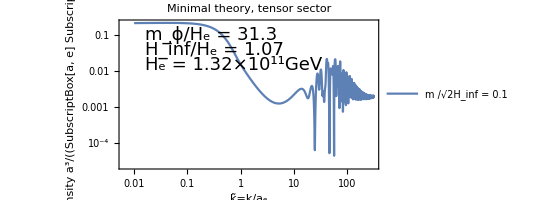

```mathematica
tensorMinimalRelicPlot=plotRelicSpectrumTensor[datMinimalRelic,βkSqrTensorMinimalRelicListList1]
```

```mathematica
βkSqrVectorMinimalRelicListList=calculateβkSqrVector[datMinimalRelic];
```

```mathematica
vectorMinimalRelicPlot=plotRelicSpectrumVector[datMinimalRelic,βkSqrVectorMinimalRelicListList];
```

```mathematica
a3nTensor=calculateTotalNumberDensity[datMinimalRelic,βkSqrTensorMinimalRelicListList];
a3nVector=calculateTotalNumberDensity[datMinimalRelic,βkSqrVectorMinimalRelicListList];
```

```mathematica
TRH=10^5 GeV;
```

```mathematica
Block[{mList=datMinimalRelic["mList"],He=datMinimalRelic["He"],ae=1},
Ωh2Tensor=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nTensor/(ae^3 He^3));
Ωh2Vector=2(0.114)(mList/(10^10 GeV))(He/(10^10 GeV))(TRH/(10^8 GeV))(a3nVector/(ae^3 He^3));
];
```

```mathematica
minimalRelicPlot=Block[{mList=datMinimalRelic["mList"],He=datMinimalRelic["He"],Hinf=datMinimalRelic["Hinf"],ae=1},
ListLogLogPlot[{
{mList/Hinf,Ωh2Tensor}ᵀ,{mList/Hinf,Ωh2Vector}ᵀ,{mList/Hinf,Ωh2Tensor+Ωh2Vector}ᵀ,
Table[{10^logm,0.12},{logm,Subdivide[0,1,14]}]},
Joined->True,
Frame->True,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
FrameLabel->{{"Ωh^2",""},{"m/H_inf","Relic Density (Minimal Theory)"}},
GridLines->Full,
PlotLegends->Placed[LineLegend[{"Tensor","Vector","T+V","Constant 0.12"},LabelStyle->{FontFamily->fontfam,FontSize->16}],{Left,Bottom}],
ImageSize->Large,
Epilog->{
Text[Style["T_RH = 10^5GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.3,0.2}],{-1,0}]
}]
]
```

#### Tests for high-k

```mathematica
Hparams={He->5.429813562888717*^-8,Hinf->5.781988559618248*^-8};
mListNormal=(√2 Hinf)/He{1.0}/.Hparams;
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,0,3,0.01}];
dat2=loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
βkSqrTensorListList2=calculateβkSqrTensor[dat2];
```

```mathematica
tensorMinimalNkHighkPlot=plotRelicSpectrumTensor[dat2,βkSqrTensorListList2];
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorMinimalNkHighk.pdf",tensorMinimalNkHighkPlot];*)
```

The time used for minimal, tensor data

```mathematica
parts={20*1000,15*1000,15*1000,18*500};
parts/(parts//Total)//N
```

{0.338983,0.254237,0.254237,0.152542}

```mathematica
3*1000+500
```

3500

```mathematica
{Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort//Length
```

891

```mathematica
20*2/0.05+15*(0.5/0.005+0.5/0.002)+18*0.5/0.001
```

15050.

```mathematica
(1+78/55)*891*17*5/6/3600//N
```

8.47875

#### Old minimal data

```mathematica
(*Hparams={He->5.429813562888717*^-8,Hinf->5.781988559618248*^-8};
mListNormal=(√2 Hinf)/He{1.0,2.0,3.0,4.0}/.Hparams;
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-3,1,0.05}];
Hash[{60,"H",100,mListNormal,kListListNormal,"Minimal"}]*)
```

```mathematica
(*datMinimal=loadDat[60,"H",100,mListNormal,kListListNormal,"Minimal"];*)
```

```mathematica
(*βkSqrTensorListListMinimal=calculateβkSqrTensor[datMinimal];
βkSqrVectorListListMinimal=calculateβkSqrVector[datMinimal];*)
```

```mathematica
(*epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[datMinimal["mϕ"]/datMinimal["He"]//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[datMinimal["Hinf"]/datMinimal["He"]//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[datMinimal["He"]/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};*)
```

```mathematica
(*tensorMinimalβkSqrPlot=ListLogLogPlot[Table[{(datMinimal["kListList"][[i]])/datMinimal["He"],βkSqrTensorListListMinimal[[i]]}ᵀ,{i,Length[datMinimal["mList"]]}],
Frame->True,
FrameLabel->{"k̃=k/(a_eH_e)","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Minimal theory, tensor sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["m /√2H_inf = "~~ToString[m/(√2 datMinimal["Hinf"])],{m,datMinimal["mList"]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full];*)
```

```mathematica
(*vectorMinimalβkSqrPlot=ListLogLogPlot[Table[{(datMinimal["kListList"][[i]])/datMinimal["He"],βkSqrVectorListListMinimal[[i]]}ᵀ,{i,Length[datMinimal["mList"]]}],
Frame->True,
FrameLabel->{"k̃=k/(a_eH_e)","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Minimal theory, vector sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["m /√2H_inf = "~~ToString[m/(√2 datMinimal["Hinf"])],{m,datMinimal["mList"]}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full];*)
```

```mathematica
(*tensorMinimalPlot=plotRelicSpectrumTensor[datMinimal,βkSqrTensorListListMinimal];
vectorMinimalPlot=plotRelicSpectrumVector[datMinimal,βkSqrVectorListListMinimal];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorMinimalNk.pdf",vectorMinimalPlot];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorMinimalBetak.pdf",vectorMinimalβkSqrPlot];*)
```

```mathematica
(*HderivSubs={H'[t]->V[ϕ[t]]/Mp^2-3 H[t]^2,H''[t]->∂_t (V[ϕ[t]]/Mp^2-3 H[t]^2),H'''[t]->∂_t ∂_t (V[ϕ[t]]/Mp^2-3 H[t]^2)}/.V->datNonMinimal["V"]//N//Simplify;*)
```

```mathematica
(*ωkSqrVExpr=(4 k^6 (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+a[t]^6 (m^2+3 H[t]^2-H'[t])^4 (4 m^2+3 H[t]^2+2 H'[t])+2 k^2 a[t]^4 (m^2+3 H[t]^2-H'[t]) (6 m^6+63 H[t]^6-8 m^2 H'[t]^2+10 H'[t]^3+12 H[t]^4 (8 m^2+H'[t])-21 H[t]^3 H''[t]-H[t] (7 m^2+17 H'[t]) H''[t]+2 H''[t]^2+m^2 H^(3)[t]-H'[t] (8 m^4+H^(3)[t])+H[t]^2 (43 m^4-20 m^2 H'[t]+31 H'[t]^2+3 H^(3)[t]))+k^4 a[t]^2 (12 m^6+99 H[t]^6+6 H[t]^4 (29 m^2-20 H'[t])-28 m^2 H'[t]^2+26 H'[t]^3-6 H[t]^3 H''[t]-2 H[t] (m^2+5 H'[t]) H''[t]+H''[t]^2+2 m^2 H^(3)[t]-2 H'[t] (5 m^4+H^(3)[t])+H[t]^2 (83 m^4-70 m^2 H'[t]-13 H'[t]^2+6 H^(3)[t])))/(4 a[t]^2 (k^2+a[t]^2 (m^2+3 H[t]^2-H'[t]))^2 (m^2+3 H[t]^2-H'[t])^2);*)
```

```mathematica
(*Plot[√ωkSqrVExpr/.HderivSubs/.datNonMinimal["bgSol"]/.{k->10^3 datNonMinimal["He"],m->0.5 √2 datNonMinimal["Hinf"]},{t,datNonMinimal["asympStart"],datNonMinimal["asympEnd"]}]*)
```

```mathematica
(*Plot[√(m^2+k^2/a[t]^2)/.datNonMinimal["bgSol"]/.{k->10^3 datNonMinimal["He"],m->0.5 √2 datNonMinimal["Hinf"]},{t,datNonMinimal["asympStart"],datNonMinimal["asympEnd"]}]*)
```

```mathematica
(*√(m^2+k^2/a[t]^2)/.datNonMinimal["bgSol"]/.t->datNonMinimal["T"]/.{k->10^2 datNonMinimal["He"],m->0.5 √2 datNonMinimal["Hinf"]}*)
```

#### Non-minimal (Old)

```mathematica
Hparams={He->5.429813562888717*^-8,Hinf->5.781988559618248*^-8};
mListNormal=(√2 Hinf)/He{1.0,2.0,3.0,4.0,5.0,6.0}/.Hparams;
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-3,1.5,0.05}];
datNonMinimal=loadDat[60,"H",100,mListNormal,kListListNormal,"Non-Minimal"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

```mathematica
βkSqrTensorListListNonMinimal=calculateβkSqrTensor[datNonMinimal];
βkSqrVectorListListNonMinimal=calculateβkSqrVector[datNonMinimal];
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {(6.68628×10^-15+3.24935×10^-19 ⅇ^Times[«2»]) χt[t]+χt''[t]==0,True,True}.

ReplaceAll::reps: {6.6866×10^-15 χt[1.03785×10^11]+χt''[1.03785×10^11]==0,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {6.6866×10^-15 χt[1.03786×10^11]+χt''[1.03786×10^11]==0,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {(6.68628×10^-15+4.09069×10^-18 ⅇ^Times[«2»]) χt[t]+χt''[t]==0,True,True}.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {(6.68628×10^-15+5.14988×10^-18 ⅇ^Times[«2»]) χt[t]+χt''[t]==0,True,True}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

```mathematica
tensorNonMinimalPlot=plotRelicSpectrumTensor[datNonMinimal,βkSqrTensorListListNonMinimal];
vectorNonMinimalPlot=plotRelicSpectrumVector[datNonMinimal,βkSqrVectorListListNonMinimal];
```

ReplaceAll::reps: {6.6866×10^-15 χt[1.03785×10^11]+χt''[1.03785×10^11]==0.,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {6.6866×10^-15 χt[1.03786×10^11]+χt''[1.03786×10^11]==0.,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*Simplify[DSolve[χ''[η]+1/η^2(m^2/He^2-2)χ[η]==0,χ,η],Assumptions->{m>0,He>0}]*)
```

```mathematica
Block[{mϕ=datNonMinimal["mϕ"],He=datMinimal["He"],Hinf=datMinimal["Hinf"],kListList=datNonMinimal["kListList"],mList=datNonMinimal["mList"],epilog},
epilog={
Text[Style["m_ϕ/H_e = "~~ToString[NumberForm[mϕ/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.9}],{-1,0}],
Text[Style["H_inf/H_e = "~~ToString[NumberForm[Hinf/He//N,3],StandardForm],{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.8}],{-1,0}],
Text[Style["H_e = "~~ToString[NumberForm[He/GeV//N,3],StandardForm]~~"GeV",{FontFamily->fontfam,FontSize->18}],Scaled[{0.1,0.7}],{-1,0}]
};
tensorNonMinimalβkSqrPlot=ListLogLogPlot[Table[{kListList[[i]]/He,βkSqrTensorListListNonMinimal[[i]]}ᵀ,{i,Length[mList]}],
Frame->True,
FrameLabel->{"k̃=k/(a_eH_e)","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Non-Minimal theory, tensor sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["m /√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full];
vectorNonMinimalβkSqrPlot=ListLogLogPlot[Table[{kListList[[i]]/He,βkSqrVectorListListNonMinimal[[i]]}ᵀ,{i,Length[mList]}],
Frame->True,
FrameLabel->{"k̃=k/(a_eH_e)","|β_k|^2"},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLabel->Style["Non-Minimal theory, vector sector",Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]],
PlotLegends->Placed[LineLegend[Table["m /√2H_inf = "~~ToString[m/(√2 Hinf)],{m,mList}],LabelStyle->{FontFamily->fontfam,FontSize->16},LegendMarkerSize->12,LegendLayout->{"Column",1},Spacings->0.25],{Right,Top}],
Epilog->epilog,
Joined->True,ImageSize->Large,GridLines->Full];
]
```

ReplaceAll::reps: {6.6866×10^-15 χt[1.03785×10^11]+χt''[1.03785×10^11]==0,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {6.6866×10^-15 χt[1.03786×10^11]+χt''[1.03786×10^11]==0,True,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

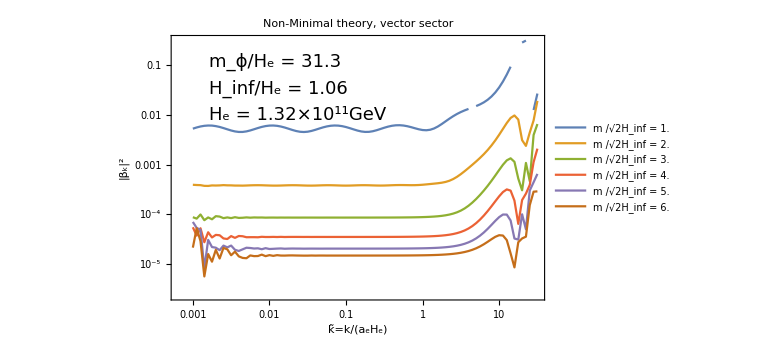

```mathematica
vectorNonMinimalβkSqrPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_tensorNonMinimalNk.pdf",tensorNonMinimalPlot];*)
```

```mathematica
(*Export[NotebookDirectory[]<>"../Plots/"<>"fig_vectorNonMinimalBetak.pdf",vectorNonMinimalβkSqrPlot];*)
```

```mathematica
(*NumericQ[datNonMinimal["VSectorχtListList"][[1,#,1]]]&/@Range[90]*)
```

```mathematica
(*NumericQ[datNonMinimal["VSectorχtListList"][[1,89,1]]]*)
```

```mathematica
(*Log[10,kListList[[1,89]]/datNonMinimal["He"]]*)
```

```mathematica
(*{datNonMinimal["kListList"][[1,89]],datNonMinimal["mList"][[1]]}*)
```

```mathematica
kListList=datNonMinimal["kListList"];
mList=datNonMinimal["mList"];
bgSol=datNonMinimal["bgSol"];
T=datNonMinimal["T"];
TSectorχtListList=datNonMinimal["TSectorχtListList"];
theory=datNonMinimal["theory"];
```

```mathematica
i=6;j=1;
```

```mathematica
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
{χtInitT,DχtInitT}=TSectorχtListList[[i,j]];
ωkSqrT=Switch[theory,
"Minimal",k^2/a[t]^2+m^2-9/4 H[t]^2-3/2 H'[t]/.kmParamSub/.bgSol,
"Non-Minimal",k^2/a[t]^2+m^2+3/4 H[t]^2+1/2 H'[t]/.kmParamSub/.bgSol];
solnT=NDSolve[{χt''[t]+ωkSqrT χt[t]==0,χt[T]==χtInitT,χt'[T]==DχtInitT},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
AbsoluteTiming[(2/(asympEnd-asympStart))NIntegrate[(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT,{t,(asympStart+asympEnd)/2,asympEnd}]]
```

{3.35369,0.0000146303}

#### Tests for all-k

```mathematica
(*Hparams={He->5.4277517240581206*^-8,Hinf->5.781988559618248*^-8};
mListNormal=(√2 Hinf)/He{1.0}/.Hparams;
kListListNormal=Table[10^x,{i,Length[mListNormal]},{x,-3,3,0.5}];
dat3=loadDat[60,"H",400,mListNormal,kListListNormal,"Minimal"];*)
```

```mathematica
(*βkSqrTensorListList3=calculateβkSqrTensor[dat3];
tensorMinimalPlotTensor3=plotRelicSpectrumTensor[dat3,βkSqrTensorListList3]*)
```

```mathematica
(*βkSqrVectorListList3=calculateβkSqrVector[dat3];
tensorMinimalPlotVector3=plotRelicSpectrumVector[dat3,βkSqrVectorListList3]*)
```

## Old combine code

Check that inflaton model, inflaton initial params, spectator model, tScale, units are consistent.

```mathematica
checkItems={"inflatonModel","Ncmb","As","tScale","theory","Mp"};
combinable=AllTrue[Table[#[item]&/@datCollection//DeleteDuplicates//Length,{item,checkItems}],#==1&];
```

Combine mListNormal and kListListNormal, output a kListListPostions to know what dat to extract χt data from

```mathematica
mListNormal=Table[dat["mListNormal"],{dat,datCollection}]//Flatten//DeleteDuplicates//Sort;
```

```mathematica
kListListPositions={};
For[i=1,i<=Length[mListNormal],i++,
kListPositions={};
For[j=1,j<=Length[datCollection],j++,
posList=Position[datCollection[[j]]["mListNormal"],mListNormal[[i]]]//Flatten;
If[Length[posList]>0,
pos=posList[[1]];
kIndices=Table[{j,pos,k},{k,Length[datCollection[[j]]["kListListNormal"][[pos]]]}];
AppendTo[kListPositions,kIndices];
];
];
kListPositionsFlattened=Flatten[kListPositions,1];
kListPositionsReduced=DeleteDuplicatesBy[kListPositionsFlattened,datCollection[[#[[1]]]]["kListListNormal"][[#[[2]],#[[3]]]]&];
kListPositionsReduced=SortBy[kListPositionsReduced,datCollection[[#[[1]]]]["kListListNormal"][[#[[2]],#[[3]]]]&];
AppendTo[kListListPositions,kListPositionsReduced];
];
```

```mathematica
kListListNormal=Table[Table[datCollection[[idx[[1]]]]["kListListNormal"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}];
```

Do data combine for each sector, assuming mListNormal and kListListNormal are sorted in increasing order

```mathematica
noNullTSector=And[Evaluate[Table[Dimensions[dat["TSectorχtListList"]]!={},{dat,datCollection}]/.List->Sequence]];
noNullVSector=And[Evaluate[Table[Dimensions[dat["VSectorχtListList"]]!={},{dat,datCollection}]/.List->Sequence]];
noNullSSector=And[Evaluate[Table[Dimensions[dat["SSectorχtListList"]]!={},{dat,datCollection}]/.List->Sequence]];
```

```mathematica
{noNullSSector,noNullVSector,noNullTSector}
```

{False,True,True}

```mathematica
TSectorχtListList=If[noNullTSector,Table[Table[datCollection[[idx[[1]]]]["TSectorχtListList"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}],Null];
VSectorχtListList=If[noNullVSector,Table[Table[datCollection[[idx[[1]]]]["VSectorχtListList"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}],Null];
SSectorχtListList=If[noNullSSector,Table[Table[datCollection[[idx[[1]]]]["SSectorχtListList"][[idx[[2]],idx[[3]]]],{idx,kListListPositions[[i]]}],{i,Length[mListNormal]}],Null];
```

```mathematica
TSectorFinal=If[noNullTSector,Flatten[TSectorχtListList,1],Null];
VSectorFinal=If[noNullVSector,Flatten[VSectorχtListList,1],Null];
SSectorFinal=If[noNullSSector,Flatten[SSectorχtListList,1],Null];
```

```mathematica
combined=combineDats[datCollection];
```

```mathematica
associationList={"Ncmb"->Ncmb,"inflatonModel"->inflatonModel,"tScale"->tScale,"theory"->theory,
"Mp"->Mp,"V"->V,"ϵv"->ϵv,"ηv"->ηv,"ϕf"->ϕf,"n"->n,"asympStart"->asympStart,"asympEnd"->asympEnd,"bgSol"->bgSol};
```

## Condition for asymptoticity: integrate or not to calculate βkSqr

#### Old βkSqr calculation module

```mathematica
calculateβkSqrTensor[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],bgSol=dat["bgSol"],TSectorχtListList=dat["TSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitT,DχtInitT,ωkSqrT,solnT},
βkSqr=Table[Table[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
{χtInitT,DχtInitT}=TSectorχtListList[[i,j]];
ωkSqrT=Switch[theory,
"Minimal",k^2/a[t]^2+m^2-9/4 H[t]^2-3/2 H'[t]/.kmParamSub/.bgSol,
"Non-Minimal",k^2/a[t]^2+m^2+3/4 H[t]^2+1/2 H'[t]/.kmParamSub/.bgSol];
solnT=NDSolve[{χt''[t]+ωkSqrT χt[t]==0,χt[T]==χtInitT,χt'[T]==DχtInitT},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
(*(1/(asympEnd-asympStart))NIntegrate[(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT,{t,asympStart,asympEnd}]*)
(*(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT/.t->T*)
Table[Evaluate[(√ωkSqrT)/2 Abs[χt[t]]^2+1/(2 √ωkSqrT)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnT],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
,{j,Length[kListList[[i]]]}],{i,Length[mList]}];
βkSqr
];
```

```mathematica
calculateβkSqrVector[dat_]:=
Module[{theory=dat["theory"],mList=dat["mList"],kListList=dat["kListList"],T=dat["T"],bgSol=dat["bgSol"],V=dat["V"],Mp=dat["Mp"],VSectorχtListList=dat["VSectorχtListList"],
βkSqr,kmParamSub,asympStart,asympEnd,χtInitV,DχtInitV,ωkSqrVExpr,ωkSqrV,Kc,cInitV,DcInitV,HderivSubs,P,Q,solnV},
βkSqr=Table[Table[
kmParamSub={k->kListList[[i,j]],m->mList[[i]]};
{asympStart,asympEnd}={T,T+(2π)/(√(k^2/a[t]^2+m^2/.kmParamSub/.bgSol/.t->T))};
Switch[theory,
"Minimal",
{χtInitV,DχtInitV}=VSectorχtListList[[i,j]];
ωkSqrV=(4 k^6+k^4 a[t]^2 (12 m^2-25 H[t]^2-10 H'[t])+2 k^2 m^2 a[t]^4 (6 m^2-11 H[t]^2-8 H'[t])+m^4 a[t]^6 (4 m^2-9 H[t]^2-6 H'[t]))/(4 a[t]^2 (k^2+m^2 a[t]^2)^2)/.kmParamSub/.bgSol;
solnV=NDSolve[{χt''[t]+ωkSqrV χt[t]==0,χt[T]==χtInitV,χt'[T]==DχtInitV},{χt},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
Table[(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.solnV,{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean,
"Non-Minimal",
Kc[t_]:=k^2 a[t]^3 (1-k^2/(k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])));
{cInitV,DcInitV}=VSectorχtListList[[i,j]];
HderivSubs={H'[t]->V[ϕ[t]]/Mp^2-3 H[t]^2,H''[t]->D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t],H'''[t]->D[D[(V[ϕ[t]]/Mp^2-3 H[t]^2), t], t]}//N//Simplify;
P=(H[t] (3 a[t]^2 (m^2+3 H[t]^2-H'[t])^2+k^2 (5 m^2+15 H[t]^2+H'[t]))-k^2 H''[t])/((k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])) (m^2+3 H[t]^2-H'[t]))/.HderivSubs/.kmParamSub/.bgSol;
Q=((k^2+a[t]^2 (m^2+3 H[t]^2-H'[t])) (m^2+3 H[t]^2+2 H'[t]))/(a[t]^2 (m^2+3 H[t]^2-H'[t]))/.HderivSubs/.kmParamSub/.bgSol;
solnV=NDSolve[{c''[t]+P c'[t]+Q c[t]==0,c[T]==cInitV,c'[T]==DcInitV},{c},{t,asympStart,asympEnd},MaxSteps->Infinity,MaxStepSize->Infinity,Method->"Adams",PrecisionGoal->10,AccuracyGoal->Infinity][[1]];
ωkSqrVExpr=(4 k^6 (m^2+3 H[t]^2-H'[t]) (m^2+3 H[t]^2+2 H'[t])+a[t]^6 (m^2+3 H[t]^2-H'[t])^4 (4 m^2+3 H[t]^2+2 H'[t])+2 k^2 a[t]^4 (m^2+3 H[t]^2-H'[t]) (6 m^6+63 H[t]^6-8 m^2 H'[t]^2+10 H'[t]^3+12 H[t]^4 (8 m^2+H'[t])-21 H[t]^3 H''[t]-H[t] (7 m^2+17 H'[t]) H''[t]+2 H''[t]^2+m^2 Derivative[3][H][t]-H'[t] (8 m^4+Derivative[3][H][t])+H[t]^2 (43 m^4-20 m^2 H'[t]+31 H'[t]^2+3 Derivative[3][H][t]))+k^4 a[t]^2 (12 m^6+99 H[t]^6+6 H[t]^4 (29 m^2-20 H'[t])-28 m^2 H'[t]^2+26 H'[t]^3-6 H[t]^3 H''[t]-2 H[t] (m^2+5 H'[t]) H''[t]+H''[t]^2+2 m^2 Derivative[3][H][t]-2 H'[t] (5 m^4+Derivative[3][H][t])+H[t]^2 (83 m^4-70 m^2 H'[t]-13 H'[t]^2+6 Derivative[3][H][t])))/(4 a[t]^2 (k^2+a[t]^2 (m^2+3 H[t]^2-H'[t]))^2 (m^2+3 H[t]^2-H'[t])^2);
ωkSqrV=ωkSqrVExpr/.HderivSubs/.kmParamSub/.bgSol;
Table[Evaluate[(√ωkSqrV)/2 Abs[χt[t]]^2+1/(2 √ωkSqrV)Abs[χt'[t]]^2-Im[χt[t]Conjugate[χt'[t]]]/.{χt->Function[t,Evaluate[√2 Kc[t]^(1/2)c[t]]]}/.atoHCoordinate/.kmParamSub/.bgSol/.solnV],{t,asympStart,asympEnd,(asympEnd-asympStart)/20}]//Mean
]
,{j,Length[kListList[[i]]]}],{i,Length[mList]}];
βkSqr
];
```

#### Old

```mathematica
(*datMinimalRelicCombined[["TSectorχtListList"]][[1]]//Dimensions*)
```

```mathematica
(*Keys[datMinimalCollection[[1]]]*)
```

```mathematica
(*Log[10,datMinimalRelicCombined["kListListNormal"][[1]]]*)
```

```mathematica
(*datMinimalRelicCombined["asympEnd"]-datMinimalRelicCombined["asympStart"]*)
```

```mathematica
(*TSectorχtListList=datMinimalRelicCombined["TSectorχtListList"];
VSectorχtListList=datMinimalRelicCombined["VSectorχtListList"];*)
```

```mathematica
(*TSectorχtListList=ReplacePart[TSectorχtListList,{1,15}->{0,0}];*)
```

```mathematica
(*VSectorχtListList=ReplacePart[VSectorχtListList,{1,38}->{0,0}];*)
```

```mathematica
(*datMinimalRelicCombined["TSectorχtListList"]=TSectorχtListList;
datMinimalRelicCombined["VSectorχtListList"]=VSectorχtListList;*)
```

```mathematica
(*mListNormal=((√2 Hinf)/He/.Hparams){0.01,0.1};
kListListNormal=Table[{Table[10^x,{x,-2,-1,0.05}],Table[10^x,{x,-1,1,0.05}],Table[10^x,{x,1,1.5,0.005}],Table[10^x,{x,1.5,2,0.002}],Table[10^x,{x,2,2.5,0.001}]}//Flatten//DeleteDuplicates//Sort,{i,Length[mListNormal]}];
tempDat=loadDat[60,"H",200,mListNormal,kListListNormal,"Minimal"];
tempDat["mList"]=tempDat["mList"][[2;;2]];
tempDat["kListList"]=tempDat["kListList"][[2;;2]];
tempDat["mListNormal"]=tempDat["mListNormal"][[2;;2]];
tempDat["kListListNormal"]=tempDat["kListListNormal"][[2;;2]];
tempDat["TSectorχtListList"]=tempDat["TSectorχtListList"][[2;;2]];
tempDat["VSectorχtListList"]=tempDat["VSectorχtListList"][[2;;2]];*)
```

```mathematica
(*Block[{bgSol=tempDat["bgSol"],asympStart=tempDat["asympStart"],asympEnd=tempDat["asympEnd"]},
Plot[H[t]/.bgSol,{t,asympStart,asympEnd}]
]*)
```

```mathematica
(*Block[{bgSol=datMinimalRelicCombined["bgSol"],asympStart=datMinimalRelicCombined["asympStart"],asympEnd=datMinimalRelicCombined["asympEnd"]},
Plot[H[t]/.bgSol,{t,asympStart,asympEnd}]
]*)
```

#### Tests

high mass (modified algo with optimized switching)

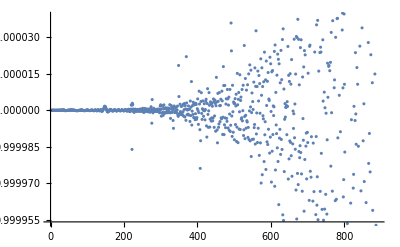

```mathematica
ListPlot[tempResult/tempResult2]
```

```mathematica
tempResult/tempResult2
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,0.999984,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,0.999995,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,0.999998,0.999999,1.,1.,0.999999,0.999998,1.,1.,1.,0.999999,0.999999,1.,1.,0.999999,0.999999,1.,1.,0.999999,1.,1.,1.,0.999999,1.,1.,0.999999,0.999997,1.,1.,0.999999,0.999999,1.,1.,0.999996,0.999993,1.,1.,0.999999,1.,1.,0.999999,1.,1.,0.999999,1.,1.,0.999998,0.999998,1.00002,1.00001,0.999998,0.999999,1.,0.999999,0.999998,1.,0.999998,0.999999,1.,0.999998,0.999999,1.,0.999998,1.,1.,0.999997,1.,1.,0.999996,1.00002,1.,0.999998,1.,1.,0.999998,1.,0.999998,1.,1.,0.999995,1.,0.999998,1.,1.00001,0.999994,1.,1.,0.999998,1.,0.999997,1.,1.,0.999997,0.999996,0.999999,1.,1.,0.999996,0.999997,1.,1.,1.,0.999994,0.999999,1.00001,1.,0.999992,0.999976,0.999987,1.,1.00001,0.999999,0.999996,1.,1.,1.,0.999998,1.,1.,1.,0.999996,1.,1.,1.,0.999994,0.999989,1.,1.00001,0.999998,0.999993,1.,1.00001,1.,0.999993,0.999996,1.,1.,0.999996,0.999997,1.,1.,0.999996,0.999997,1.,1.,0.999993,0.999998,1.,1.,0.999991,1.,1.00001,1.,0.999992,0.999987,1.00001,1.,0.999993,0.999994,1.00001,1.,0.999995,1.,1.,0.999997,0.999997,1.00001,1.,0.99999,0.999997,1.00002,1.00001,0.99999,0.999994,1.00001,0.999997,0.999993,1.,1.,0.999997,0.999995,1.00001,1.,0.999993,1.,1.00001,0.999992,0.999998,1.00001,0.999991,0.999994,1.00004,1.00002,0.999998,0.999989,1.00001,0.999999,0.999991,1.,1.,0.999988,1.,1.,0.999994,1.,1.00001,0.999987,0.999993,1.00002,1.,0.999987,1.,1.00001,0.999992,0.999999,1.00001,0.999992,1.,1.00001,0.999996,0.999997,1.00001,0.999996,1.,1.00001,0.99999,0.999992,1.00003,0.999997,0.999988,1.00001,0.999998,0.999993,1.00001,0.999996,0.999995,1.00001,0.999989,0.999993,1.00001,0.999988,1.,1.00002,0.999987,1.,1.00002,0.999981,0.999999,1.00001,0.999988,1.,1.,0.999988,1.00001,0.999993,0.999994,1.00002,0.999986,1.00001,1.00003,0.99999,0.999999,1.00001,0.999987,1.00002,0.999993,1.,1.00001,0.999981,1.00001,0.999999,0.999987,1.00002,0.99997,1.00001,1.00002,0.999974,1.00001,0.999998,0.999997,1.00001,0.999979,1.00002,0.99999,0.999995,1.00001,0.999976,1.00002,1.,0.999987,1.00001,0.999986,1.00002,0.999992,1.,1.,0.999982,1.00002,0.999989,1.00002,1.,0.99997,1.00002,0.999983,1.00002,0.99999,1.,0.999998,1.,1.00002,0.999969,1.00003,0.999975,1.00001,0.999994,0.99999,1.00001,0.999985,1.00002,0.999979,1.00002,0.999961,1.00002,0.999989,0.999992,1.00001,0.999982,1.00002,0.999988,1.00001,0.999984,1.00003,0.999957,1.00003,0.999955,1.00001,0.999975,0.999996,1.,0.999997,1.,1.,1.,0.99999,1.,1.,1.00003,0.999972,1.00001,0.99998,1.00001,0.999987,1.00002,0.999987,1.00001,0.999981,1.00002,0.999973,1.00005,0.999986,1.,0.999993,0.999999,1.00003,0.999989,1.,0.999984,1.00001,0.999967,1.00003,0.999955,1.00003,0.999974,1.00004,0.999969,1.00003,0.999983,1.00001,0.999981,0.999985,1.00003,0.999983,1.00003,0.999974,1.00006,0.999967,1.00001,0.999997,0.999988,1.00002,0.999959,1.00002,0.99998,1.00002,1.00004,0.999985,0.999991,0.999972,1.00004,0.999991,0.999987,1.00002,0.999921,1.00004,0.999963,1.00003,1.00003,0.999975,1.00005,0.999972,0.999989,1.00008,0.999942,1.00005,0.999963,0.999987,1.00005,0.999967,1.00006,1.00002,0.99992,1.00006,0.999957,0.999989,1.00004,0.999961,0.999973,1.00004,0.999955,1.00006,1.00002,0.999949,1.00007,1.00002,0.999967,1.00003,1.00002,0.999982,1.00007,0.999959,0.999944,1.00003,1.,0.999955,1.00005,1.00001,0.999959,1.,1.00005,0.999965,0.999999,1.00006,0.999957,0.999988,1.00002,1.00001,0.999886,1.00002,1.00002,0.999905,1.00002,1.00005,1.00002,0.999977,1.00003,0.999999,0.999927,0.999967,1.00004,1.00006,0.99992,0.999944,1.00001,1.00001,0.999912,0.999963,1.00003,1.00011,0.999963,0.999889,1.00004,1.00004,0.999989,0.99994,1.00005,1.00007,1.00001,0.999927,0.999924,0.999991,1.00007,1.00011,0.999851,0.999926,1.00003,1.00004,1.00001,0.999964,0.999971,1.00004,1.00001,0.999983,0.999935,0.999868,1.00004,1.00007,1.00011,1.00005,0.999953,0.999929,0.999936,1.00012,1.00011,1.00005,1.00005,0.999927,0.999809,0.999962,1.00011,0.999996,1.00017,1.00005,0.999913,0.99989,0.999968,0.999974,1.,1.00006,1.00025,0.999996,1.00002,0.999999,0.999986,0.999938,1.00002,0.999906,1.00001,0.999929,0.999985,0.999806,1.00004,1.00013,1.00003,1.00009,1.00015,0.999967,0.99985,0.999947,1.00003,0.999844,0.9999,0.999987,0.99988,1.,0.999971,0.999901,1.00006,1.0001,0.999881,0.999962,1.00005,0.999949,0.999869,0.999951,0.999852,1.00003,0.999978,0.999747,0.99999,0.999791,0.999975,0.999944,1.00002,0.999893,0.999883,0.999916,1.00001,0.999959,1.00034,0.999943,0.99986,0.999904,0.999883,1.00001,0.999597,0.999779,0.999953,0.999845,0.999699,0.999886,1.00041}}

Higuchi bound (modified algo with optimized switching)

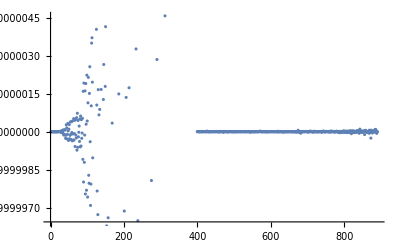

```mathematica
ListPlot[tempResult/tempResult2]
```

```mathematica
tempResult/tempResult2
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,0.999999,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,0.999999,1.,1.,1.,1.,0.999999,1.,0.999998,1.,0.999999,1.,1.,0.999998,1.,1.,0.999998,1.,1.,0.999997,1.,1.,0.999998,0.999998,1.,1.,1.,0.999997,0.999998,1.,1.,1.,1.,0.999999,0.999996,0.999992,0.999986,0.999977,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,0.999998,0.999995,0.999997,1.,1.00001,1.,0.999993,1.,1.00001,0.99999,1.,1.,0.999994,1.00001,0.999993,1.00001,0.999995,1.,1.,0.999994,1.00001,0.999994,1.,1.,0.999991,1.00001,0.999996,0.999994,1.00001,0.999989,0.999997,1.00002,0.999985,0.999994,1.00002,0.999988,0.99999,1.00002,0.999994,0.999985,1.00002,1.,0.99998,1.00002,1.00001,0.999974,1.00001,1.00002,0.999972,0.999994,1.00003,0.999989,0.999975,1.00002,1.00002,0.999984,0.999979,1.00001,1.00002,1.,0.999978,0.999984,1.00001,1.00002,1.00001,0.999991,0.999984,0.999994,1.00001,1.00001,1.00001,0.999996,0.999988,0.999989,0.999997,1.00001,1.00001,1.00001,1.00001,1.,0.999993,0.999987,0.999984,0.999984,0.999987,0.999991,0.999996,1.,1.00001,1.00001,1.00002,1.00003,1.00003,1.00004,1.00006,1.00008,1.00012,1.00019,1.00037,1.00026,1.00014,1.00009,1.00007,1.00005,1.00004,1.00002,1.,0.999987,0.999975,0.99997,0.999977,0.999996,1.00002,1.00003,1.00002,0.999989,0.999965,0.999972,1.00001,1.00004,1.00003,0.999992,0.999957,0.999973,1.00003,1.00004,0.999987,0.999954,1.00001,1.00004,0.999984,0.999966,1.00003,1.00002,0.999957,1.00001,1.00005,0.999935,1.00001,1.00009,0.999784,1.0003,1.0004,1.00004,0.999914,1.00008,0.99995,1.00002,0.999998,0.999986,1.00002,0.999968,1.00004,0.999962,1.00004,0.999957,1.00005,0.999947,1.00006,0.999933,1.00007,0.999938,1.00004,1.,0.999948,1.0001,0.999875,1.00013,0.999912,1.00001,1.00009,0.999855,1.00008,1.00005,0.999898,1.00003,1.00007,0.999943,0.999944,1.00007,1.00007,0.999928,0.999892,1.00005,1.00014,1.,0.999863,0.999882,1.00002,1.00016,1.00024,1.00015,0.999748,0.999733,0.999905,0.999989,1.00002,1.00004,1.00004,1.00003,1.00002,1.00001,0.999981,0.999928,0.999836,0.99976,0.99976,0.999744,0.999742,0.999794,0.999924,1.00012,1.00025,1.00016,0.999914,0.999796,0.99995,1.00018,1.00011,0.999806,0.999937,1.00022,0.999927,0.999765,1.00044,1.00028,0.999398,1.00008,1.00011,0.999814,1.00022,0.999763,1.00025,0.999762,1.00022,0.999772,1.00028,0.999582,1.00061,0.999366,1.00049,0.999627,1.00019,1.00012,0.999611,1.00035,1.00001,0.999682,1.00016,1.00033,0.999864,0.999438,1.00029,1.00072,0.999606,0.999518,0.999727,0.999959,1.00017,1.00039,1.00057,1.00057,1.00047,1.00047,1.00056,0.999414,1.00055,0.999522,1.00044,0.999545,1.00049,0.999463,1.00057,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

Higuchi bound mass result (modified asymp)

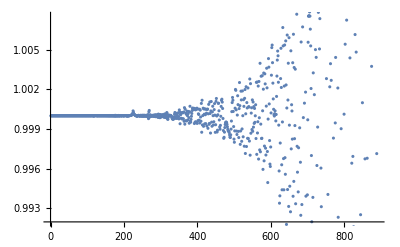

```mathematica
ListPlot[tempResult/tempResult2]
```

Higuchi bound mass result

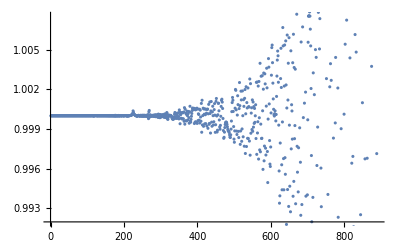

```mathematica
ListPlot[tempResult/tempResult2]
```

high mass result

```mathematica
ListPlot[tempResult/tempResult2]
```

-Graphics-

low mass result

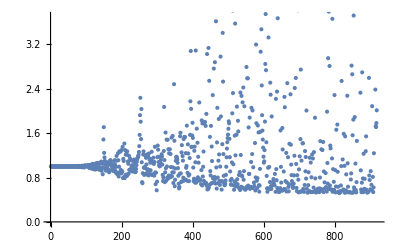

```mathematica
ListPlot[tempResult/tempResult2]
```

```mathematica
calculateβkSqrTensorTemp[datMinimalRelicCombined]
```

{{5.03025×10^8}}

```mathematica
10*19*9
```

1710

```mathematica
{datMinimalRelicCombined["kListList"][[6,400]],datMinimalRelicCombined["mList"][[6]],datMinimalRelicCombined["HT"],datMinimalRelicCombined["aT"]}
```

{5.54141×10^-6,8.17697×10^-8,3.21317×10^-12,676.419}

```mathematica
idx=6;idx2=300;
{datMinimalRelicCombined["kListList"][[idx,idx2]],datMinimalRelicCombined["mList"][[idx]],(datMinimalRelicCombined["kListList"][[idx,idx2]])/datMinimalRelicCombined["aT"]/datMinimalRelicCombined["mList"][[idx]]}
```

{3.5696×10^-6,8.17697×10^-8,0.0645375}

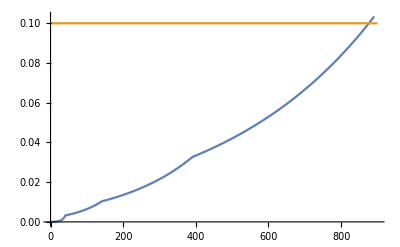

```mathematica
idx=8;
ListPlot[{(datMinimalRelicCombined["kListList"][[idx]])/datMinimalRelicCombined["aT"]/datMinimalRelicCombined["mList"][[idx]],
Table[0.1,{j,900}]},Joined->True]
```

```mathematica
(5.5*10^-6)/676//N
```

8.13609×10^-9

```mathematica
datMinimalRelicCombined["mList"][[19]]
```

1.79893×10^-6